```mathematica
(*List of some of the non-function global variables in this notebook*){ν,klist,valv,prec,prec1,prec2,tt,sdpboutput}
```

```mathematica
(*Description of a likely next step in the code: Several functions in this notebook accept a list of twist spin pairs. An example of such a list is {{7/5,0},{3/2,0},{101/100,2},{11/10,2}}. Examples of functions that accept lists of twist spin pairs include TableOfDerivs, Bfunc, CombinedFunc etc. The function TwistSpinPairs generates these. it accepts a variable, f, that indicates the increment in twist from one twist to another. However f should probably be a list of increments so the increment can be smaller when it needs to be and bigger in less vital regions to save computation time.*)(*Make sure to run SDPB wrapper before running this code.*)(*Thanks to Simon Caron-Huet, Anh-Khoi Trinh, and Clement Virally.*)
```

# Equations With s and ξ

```mathematica
ν=1/2; (*Remember that ν=(d/2)-1 => 2(nu+1)=d*)
```

```mathematica
Ci[Δ_,l_]:=Δ(Δ-(2*ν+2))+l(l+(2*ν+2)-2)(*function that will be used in A's*)
```

```mathematica
GammaP[En_,j_]:=(En+j)^2(j+2*ν)/(2*(j+ν))(*function that will be used in A's*)
```

```mathematica
GammaM[En_,j_]:=j*(En-j-2*ν)^2/(2*(j+ν))(*function that will be used in A's*)
```

```mathematica
A[n_,j_,l_]:=A[n,j,l]=Factor[(GammaP[Δ+n-1,j-1]*A[n-1,j-1,l]+GammaM[Δ+n-1,j+1]*A[n-1,j+1,l])/(Ci[Δ+n,j]-Ci[Δ,l])]
A[0,j_,l_]:=KroneckerDelta[j-l,0](*Check this.*)
```

```mathematica
P[En_,j_,s_,ξ_]:=(s^En*((j*Boole[j>-1])!))/Pochhammer[2*ν,j*Boole[j>-1]]*(GegenbauerC[j,ν,ξ])*Boole[j≥0]
```

```mathematica
G[{Δ1_,l1_},s_,ξ_,q_]:=Sum[A[n,l1+k,l1]*(P[Δ1+n,l1+k,s,ξ]),{n,0,q},{k,If[OddQ[n],Max[-n,-l1+1],Max[-n,-l1]],n,2}]/.{Δ:>Δ1,l:>l1}(*Conformal blocks*)
```

```mathematica
D0[s_,ξ_][expn_]:=(s^2*D[expn,{s,2}]+(2*ν+1)(ξ*D[expn,ξ]-s*D[expn,s])-(1-ξ^2)*D[expn,{ξ,2}])(*Operator D0 found in 2.23*)
```

```mathematica
D1[s_,ξ_][expn_]:=s(-ξ*s^2*D[expn,{s,2}]+2(1-ξ^2)s*D[expn,s,ξ]-ξ*s*D[expn,s]-(2*ν+ξ^2)*D[expn,ξ]+ξ(1-ξ^2)D[expn,{ξ,2}])(*operator D1 found in 2.23*)
```

```mathematica
D2[s_,ξ_][expn_]:=D0[s,ξ][expn]+D1[s,ξ][expn] (*Operator D in 2.23*)
```

# Equations with z and zb

```mathematica
Dz[z_,zb_][expn_]:=2*(z^2*(1-z)*D[expn,{z,2}]-z^2 D[expn,z]+zb^2*(1-zb)*D[expn,{zb,2}]-zb^2*D[expn,zb]+(2*ν*z*zb/(z-zb))*((1-z)D[expn,z]-(1-zb)*D[expn,zb]))(*Operator D found in 2.21*)
```

```mathematica
Pcomplex[En_,j_,z_,zb_]:=(Sqrt[z*zb]^En*((j*Boole[j>-1])!))/Pochhammer[2*ν,Boole[j>-1]*j]*(GegenbauerC[j,ν,(z+zb)/(2*Sqrt[z*zb])])(*Leading to equation for conformal blocks using z and zb*)
```

```mathematica
DerivsOfPcomplex[{x_,y_},z_,zb_,j_]:=DerivsOfPcomplex[{x,y},z,zb,j]=(2^(-En))*Expand[D[Pcomplex[En,j,z,zb]/(2^(-En)),{z,x},{zb,y}]/.{z:>1/2,zb:>1/2(*,En:>twist+l*)}](*keep En symbolic*)(*Idea is to store . . .*)(*Make sure that new code agrees with old code.*)(**)
```

```mathematica
{DerivsOfPcomplex[{3,4},z,zb,6]/.En:>3,D[Pcomplex[3,6,z,zb],{z,3},{zb,4}]/.{z:>1/2,zb:>1/2}}(*matching as expected*)
```

{11475/2,11475/2}

```mathematica
Expand[DerivsOfPcomplex[{2,3},z,zb,4]/(2^(-En))](*Simple polynomial in En, as desired.*)
```

-420-55 En+104 En^2-8 En^4+En^5

```mathematica
GcomplexLessOld[{twist_,l1_},z_,zb_,Δϕ_,q_]:=GcomplexLessOld[{twist,l1},z,zb,Δϕ,q]=Sum[A[n,l1+k,l1]*(Pcomplex[twist+l1+n,l1+k,z,zb]),{n,0,q},{k,If[OddQ[n],Max[-n,-l1+1],Max[-n,-l1]],n,2}]/.{Δ:>twist+l1,l:>l1}
```

```mathematica
GcomplexLessOldNormed[{twist_,l1_},z_,zb_,Δϕ_,q_]:=GcomplexLessOldNormed[{twist,l1},z,zb,Δϕ,q]=N[(Pochhammer[1,l1]/Pochhammer[1/2,l1])GcomplexLessOld[{twist,l1},z,zb,Δϕ,q],200](*This function is useful for experiments.*)
```

```mathematica
Gcomplex[{x_,y_},{twist_,l1_},1/2,1/2,Δϕ_,q_]:=Gcomplex[{x,y},{twist,l1},1/2,1/2,Δϕ,q]=N[Sum[ A[n,l1+k,l1]*(DerivsOfPcomplex[{x,y},z,zb,l1+k])/.En:>twist+l1+n,{n,0,q},{k,If[OddQ[n],Max[-n,-l1+1],Max[-n,-l1]],n,2}]/.{Δ:>twist+l1,l:>l1},200](*This is a formula for conformal blocks and their derivs with optimized DerivsOfPcomplex for faster computation*)
```

```mathematica
GcomplexNormed[{x_,y_},{twist_,l1_},1/2,1/2,Δϕ_,q_]:=GcomplexNormed[{x,y},{twist,l1},1/2,1/2,Δϕ,q]=(Pochhammer[1,l1]/Pochhammer[1/2,l1])*Gcomplex[{x,y},{twist,l1},1/2,1/2,Δϕ,q]/.l:>l1
```

```mathematica
GcomplexNormedFast[{x_,y_},{twist_,l_},1/2,1/2,Δϕ_,q_]:=derivsOfGcomplexNormed[[1+If[l==0,0,If[l==2,77,0]+If[l==4,138,0]+If[l==6,179,0]+If[l==8,200,0]]+If[l==0,(twist-(7/5))*10,(twist-1)*10]]][[1+Sum[(12-i),{i,1,x}]+y]](*This works but now I realize what the fast way to do it is. when I store derivsOfGcomplexNormed I need to have it in human friendly form. then this becomes way easier.*)
```

```mathematica
(*l=0 for 77 collumns*)
(*l=2 from column 78 to column 138*)
(*l=4 from column 139 to column 179*)
(*l=6 from column 180 to column 200*)
(*l=8 for column 201 only.*)
```

```mathematica
(*GcomplexNormedFastAttempt[{x_,y_},{twist_,l_},1/2,1/2,Δϕ_,q_]:=GcomplexNormedFastAttempt[{x,y},{twist,l},1/2,1/2,Δϕ,q]=derivsOfGcomplexNormed[[1+If[l==0,0(**(9-(14/10))/(1/10)*),If[l==2,(9-l)*10,0]+If[l==4,(9-2)*10+(9-l)*10,0]+If[l==6,(9-2)*10+(9-4)*10+(9-l)*10,0]+If[l==8,(9-2)*10+(9-4)*10+(9-6)*10+(9-l)*10,0]]+If[l==0,(twist-(7/5))*10,(twist-1)*10]]][[(11-y)*x+y]]*)(*This could be useful later.*)
```

```mathematica
Fpolynomial[{m_,n_},{twist_,j_},Δϕ_,dim_,keptPoles_,order_]:=Fpolynomial[{m,n},{twist,j},Δϕ,dim,keptPoles,order]=D[((1-z)(1-zb))^Δϕ Gstem[{twist,j},{z,zb},dim,keptPoles,order]-(z*zb)^Δϕ Gstem[{twist,j},{1-z,1-zb},dim,keptPoles,order],{z,m},{zb,n}]/.{Derivative[{0,0},{m,n},0,0,0][Gstem][{twist,j},{1-z,1-zb},dim,keptPoles,order]:>If[OddQ[m+n],-GcomplexPolynomial[{m,n},{twist,j},dim,keptPoles,order],GcomplexPolynomial[{m,n},{twist,j},dim,keptPoles,order]],Derivative[{0,0},{m,n},0,0,0][Gstem][{twist,j},{z_,zb_},dim,keptPoles,order]:>GcomplexPolynomial[{m,n},{twist,j},dim,keptPoles,order],Gstem[{twist,j},{z,zb},3,9,10]:>GcomplexPolynomial[{0,0},{twist,j},3,9,10]}/.{z:>1/2,zb:>1/2}(*This is not working well for some reason.*)
```

# Polynomials

```mathematica
directory=NotebookDirectory[]
```

/Users/michaelvenier-karzis/Desktop/Summer_2021_Research_Project/

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
prec = 400;(*Precision for Mathematica computations*)
rCrossing = N[3-2Sqrt[2],prec];(*Important constant*)
```

```mathematica
SBuseThreads = 4; (*Number of computer threads used by scalar_blocks*)
SBbinprec = 1000;(*Precision to be used by the scalar_blocks program in binary terms*)
```

Two options: either to run using locally available executable, or using Docker

```mathematica
UseDocker=False
```

False

```mathematica
(* docker version *)
If[UseDocker,
dockerExec="/Applications/Docker.app/Contents/Resources/bin/docker";
scalarBlocksPath={dockerExec,"run","-v",Directory[]~~":/usr/local/share/scalar_blocks","wlandry/sdpb:2.4.0",
"scalar_blocks"};
scalarBlocksoutputprefix="/usr/local/share/scalar_blocks/";
scalarBlocksoutputDirectory = "data_files/blocks"; 
,
(* locally compiled version: path to executable; output directory should already exist. *)
scalarBlocksPath = {"./scalar_blocks"};(*Why is there a ./ here?*)
scalarBlocksoutputprefix="";
scalarBlocksoutputDirectory = datadirectory; ]
```

```mathematica
(*Runs the scalar_blocks program once given all necessary parameters*)
runSingleScalarBlocks[js_,Δ12_,Δ34_,dim_,nmax_,keptPoles_,order_]:=RunProcess[scalarBlocksPath~Join~{"--dim",dim,"--max-derivs",nmax,"--spin-ranges",StringReplace[ToString[js],"{"|"}"->""],
"--order",order,"--poles",keptPoles,(*"--output-poles",*)
"--delta-12",Δ12,"--delta-34",Δ34,"--precision",SBbinprec,"--num-threads",SBuseThreads,"-o",scalarBlocksoutputprefix~~scalarBlocksoutputDirectory}];
```

```mathematica
(*Obtains the name of the file for a give spin that contains the zzbDeriv[m,n] objects, using the naming scheme used by scalar_blocks. Needed to properly import scalar_blocks data.*)
fileName[dim_,nmax_,l_,order_,keptPoles_,Δ12_,Δ34_]:= StringJoin[scalarBlocksoutputDirectory,"","zzbDerivTable-d",ToString[dim],"-delta12-",ToString[Δ12],"-delta34-",ToString[Δ34],"-L",ToString[l],"-nmax",ToString[nmax],"-keptPoleOrder",ToString[keptPoles],"-order",ToString[order],".m"]
```

```mathematica
(*Obtains the table of derivatives of the conformal blocks as a function of spin. set zzbDerivRule[spin] and polesList[spin] for each spin. *)
getzzbDerivTable[js_,Δ12_,Δ34_,dim_,nmax_,keptPoles_,order_]:=Module[{spinFile},
ClearAll[zzbDerivRule,polesList];
(*Running the scalar_blocks program*)
SBoutput=runSingleScalarBlocks[js,Δ12,Δ34,dim,nmax,keptPoles,order];
(*For each spin, we retrieve the proper conformal blocks output, as a rule for zzbDeriv[m,n,j] = \partial_z^m \partial_z^n of spin-j block. Should the 2nd z be a zb here?*)
Flatten@Table[spinFile = fileName[dim,nmax,j,order,keptPoles,Δ12,Δ34];
(* result are polynomials in x=del-(j+dim-2) *)
(* rescale by Pochhammers to convert to my normalization conventions [SCH] *)
rescaling=If[MatchQ[dim,2],2/(1+KroneckerDelta[j,0]),Pochhammer[(dim-2),j]/Pochhammer[(dim-2)/2,j]];
got=Get[spinFile];
Thread[(First/@#/.{zzbDeriv[n_,m_]:> zzbDeriv[n,m,j]})->rescaling*Last/@#]&[got],{j,js}]
]
```

```mathematica
(* The location of the poles in Delta in a conformal block, where order specifies how many poles, taken from code by David Simmons-Duffin*)
cbPoles[nu_,L_,order_]:=Join[
Table[-(n+L-1),{n,order}],
Table[-(-nu+k-1),{k,(order)/2}],
Table[-(-L-2nu+n-1),{n,Min[order,L]}]
];(*order is kept pole order.*)
```

# GcomplexPolynomial

```mathematica
Clear[tt]
```

```mathematica
tt=getzzbDerivTable[{0,2,4,6,8},0,0,3,11,9,10](*Substitution rules for GcomplexPolynomial. Parameters are: list of spins that can be computed = {0,2,4,6,8}, dim = 3, number of derivs that can be computed = 11. if you want more derivs then change 11. if you want more spins then add even numbers to the list.*)
```

{1}
 |  |  |  |

```mathematica
Clear[GcomplexPolynomial]
```

```mathematica
GcomplexPolynomial[{m_,n_},{twist_,j_},dim_,keptPoles_,order_]:=GcomplexPolynomial[{m,n},{twist,j},dim,keptPoles,order]=(((4*rCrossing)^(twist+j))*(zzbDeriv[n,m,j]/.tt)/Product[twist+j-i,{i,cbPoles[1/2,j,9]}])/.x:>twist+j-(j+dim-2)(*always set d=3, keptPoles=9, order=10*)(*Only computes derivs satisfying m<n and m+n=odd number*)
```

```mathematica
GcomplexPolynomial[{10,11},{10,8},3,9,10](*A maximal deriv order example. Should give ~4.62152x10^26.*)
```

4.62151959335370850344956835075083733080301032254960256986788714151186828295845977770866814186613845326820111186023024487494354803387131795540513818159082955972970883051865725895958444915028712671554304703121710715006521032462222424327064383843371468451312747971432563470137884532394526497594207633131033780896119740654001534550870335723832048×10^26

# Implicit Tables Of Derivs

```mathematica
NonZeroTableFixedSpin[l_,twistMax_,f_]:=Module[{table=Table[{twist,l},{twist,1+f,twistMax,f}]},PrependTo[table,{101/100,l}]](*We want to get close to twist=1 but avoid it because it yeild division by 0 for polynomial code.*)
NonZeroTable[twistMax_,lmax_,f_]:=Flatten[Table[NonZeroTableFixedSpin[l,twistMax,f],{l,2,lmax,2}],{{1,2},{3}}]
ZeroTable[Δϵ_,twistMax_,f_]:=Table[{twist,0},{twist,Δϵ,twistMax,f}](*These 3 functions build to TwistSpinPairs*)
```

```mathematica
TwistSpinPairs[Δϵ_,{twistMax_,lmax_},f_]:=Join[ZeroTable[Δϵ,twistMax,f],NonZeroTable[twistMax,lmax,f]](*lmax=0 yeilds errors. if lmax=0 desired then use ZeroTable.*)
```

```mathematica
(*For variable increments. Now f is a list of increments and twistMax is no longer needed.*)NonZeroTableFixedSpinVariedIncrement[l_,f_]:=Module[{table=Table[{twist,l},{twist,Table[1+(i^0)*Sum[f[[j]],{j,1,i}],{i,1,Length[f]}]}]},PrependTo[table,{101/100,l}]](*We want to get close to twist=1 but avoid it because it yeild division by 0 for polynomial code.*)
NonZeroTableVariedIncrement[lmax_,f_]:=Flatten[Table[NonZeroTableFixedSpinVariedIncrement[l,f],{l,2,lmax,2}],{{1,2},{3}}]
ZeroTableVariedIncrement[Δϵ_,f_]:=Module[{table=NonZeroTableFixedSpinVariedIncrement[0,f]/.{x_,0}:>If[x<Δϵ,Nothing,{x,0}],table2},table2=DeleteDuplicates[PrependTo[table,{Δϵ,0}]];table2](*These 3 functions build to TwistSpinPairsVariedIncrement*)
```

```mathematica
TwistSpinPairsVariedIncrement[Δϵ_,lmax_,f_]:=Join[ZeroTableVariedIncrement[Δϵ,f],NonZeroTableVariedIncrement[lmax,f]]
```

```mathematica
(*An example*)TwistSpinPairsVariedIncrement[1.4,2,{0.1,2,4.552,3,0.08}]
```

{{1.4,0},{3.1,0},{7.652,0},{10.652,0},{10.732,0},{101/100,2},{1.1,2},{3.1,2},{7.652,2},{10.652,2},{10.732,2}}

```mathematica
(*building up to fGenerator*)fGeneratorBeforeNeighbourhood[twistCritical_,neighbourhood_,largeIncrement_]:=Module[{table={},table1},While[1+Sum[table[[i]],{i,1,Length[table]}]≤twistCritical-neighbourhood-largeIncrement,AppendTo[table,largeIncrement]];AppendTo[table,twistCritical-neighbourhood-1-Sum[table[[i]],{i,1,Length[table]}]];table1=table/.table[[-1]]:>If[table[[-1]]<10^-10,Nothing,table[[-1]]]]
(*fGeneratorDuringNeighbourhoodOld[neighbourhood_,smallIncrement_]:=Module[{table=Table[(i^0)*smallIncrement,{i,1,If[IntegerQ[2*neighbourhood/smallIncrement],2*neighbourhood/smallIncrement,Round[-(1/2)+2*neighbourhood/smallIncrement]]}],table1},AppendTo[table,2*neighbourhood-1-Sum[table[[i]],{i,1,Length[table]}]];table1=table/.table[[-1]]:>If[table[[-1]]<10^-10,Nothing,table[[-1]]]]*)(*turns out to be less clean I think*)
fGeneratorDuringNeighbourhood[neighbourhood_,smallIncrement_]:=Module[{table={},table1},While[Sum[table[[i]],{i,1,Length[table]}]≤2*neighbourhood-smallIncrement,AppendTo[table,smallIncrement]];AppendTo[table,2*neighbourhood-Sum[table[[i]],{i,1,Length[table]}]];table1=table/.table[[-1]]:>If[table[[-1]]<10^-10,Nothing,table[[-1]]];table1]
fGeneratorAfterNeighbourhood[twistMax_,twistCritical_,neighbourhood_,largeIncrement_]:=Module[{table={},table1},While[Sum[table[[i]],{i,1,Length[table]}]≤twistMax-twistCritical-neighbourhood-largeIncrement,AppendTo[table,largeIncrement]];AppendTo[table,twistMax-twistCritical-neighbourhood-Sum[table[[i]],{i,1,Length[table]}]];table1=table/.table[[-1]]:>If[table[[-1]]<10^-10,Nothing,table[[-1]]];table1]
```

```mathematica
(*A convenient way to generate f lists to enter to TwistSpinPairs. The idea is to use this as a shortcut to generate a list of twistSpinPairs that has a large increment for low twists then a small increment in a neighbourhood around some critical twist then a large increment after the neighbourhood until twistMax.*)fGenerator[twistMax_,twistCritical_,neighbourhood_,smallIncrement_,largeIncrement_]:=Join[fGeneratorBeforeNeighbourhood[twistCritical,neighbourhood,largeIncrement],fGeneratorDuringNeighbourhood[neighbourhood,smallIncrement],fGeneratorAfterNeighbourhood[twistMax,twistCritical,neighbourhood,largeIncrement]]
```

```mathematica
fGenerator[20.12,10.3,1.2,0.147,0.461](*An example fGenerator. See it applied in a TwistSpinPairs in the example below. The numbers that occur only once are there to ensure the entire critical neibourhood (including boundaries) is contained in the twistSpinPairs. See next example for further explanation.*)
```

{0.461,0.461,0.461,0.461,0.461,0.461,0.461,0.461,0.461,0.461,0.461,0.461,0.461,0.461,0.461,0.461,0.461,0.263,0.147,0.147,0.147,0.147,0.147,0.147,0.147,0.147,0.147,0.147,0.147,0.147,0.147,0.147,0.147,0.147,0.048,0.461,0.461,0.461,0.461,0.461,0.461,0.461,0.461,0.461,0.461,0.461,0.461,0.461,0.461,0.461,0.461,0.461,0.461,0.322}

```mathematica
TwistSpinPairsVariedIncrement[1.5,2,fGenerator[20.12,10.3,1.2,0.147,0.461]](*Applying the above fGenerator to TwistSpinPairs. Notice that the boundaries of the critical neighbourhood (ie the interval [twistCritical-neighbourhood,twistCritical+neighbourhood]) are contained, thus we have the entire critical neighbourhood.*)
```

{{1.5,0},{1.922,0},{2.383,0},{2.844,0},{3.305,0},{3.766,0},{4.227,0},{4.688,0},{5.149,0},{5.61,0},{6.071,0},{6.532,0},{6.993,0},{7.454,0},{7.915,0},{8.376,0},{8.837,0},{9.1,0},{9.247,0},{9.394,0},{9.541,0},{9.688,0},{9.835,0},{9.982,0},{10.129,0},{10.276,0},{10.423,0},{10.57,0},{10.717,0},{10.864,0},{11.011,0},{11.158,0},{11.305,0},{11.452,0},{11.5,0},{11.961,0},{12.422,0},{12.883,0},{13.344,0},{13.805,0},{14.266,0},{14.727,0},{15.188,0},{15.649,0},{16.11,0},{16.571,0},{17.032,0},{17.493,0},{17.954,0},{18.415,0},{18.876,0},{19.337,0},{19.798,0},{20.12,0},{101/100,2},{1.461,2},{1.922,2},{2.383,2},{2.844,2},{3.305,2},{3.766,2},{4.227,2},{4.688,2},{5.149,2},{5.61,2},{6.071,2},{6.532,2},{6.993,2},{7.454,2},{7.915,2},{8.376,2},{8.837,2},{9.1,2},{9.247,2},{9.394,2},{9.541,2},{9.688,2},{9.835,2},{9.982,2},{10.129,2},{10.276,2},{10.423,2},{10.57,2},{10.717,2},{10.864,2},{11.011,2},{11.158,2},{11.305,2},{11.452,2},{11.5,2},{11.961,2},{12.422,2},{12.883,2},{13.344,2},{13.805,2},{14.266,2},{14.727,2},{15.188,2},{15.649,2},{16.11,2},{16.571,2},{17.032,2},{17.493,2},{17.954,2},{18.415,2},{18.876,2},{19.337,2},{19.798,2},{20.12,2}}

```mathematica
NonZeroTableFixedSpinHighDelta[l_,twistMax_,f_]:=Module[{table=Table[{twist,l},{twist,1+f,twistMax,f}]},PrependTo[table,{101/100,l}];AppendTo[table,{100,l}];AppendTo[table,{200,l}]]
NonZeroTableHighDelta[twistMax_,lmax_,f_]:=Flatten[Table[NonZeroTableFixedSpinHighDelta[l,twistMax,f],{l,2,lmax,2}],{{1,2},{3}}]
ZeroTableHighDelta[Δϵ_,twistMax_,f_]:=Module[{table=ZeroTable[Δϵ,twistMax,f]},AppendTo[table,{100,0}];AppendTo[table,{200,0}]]
```

```mathematica
TwistSpinPairsHighDelta[Δϵ_,{twistMax_,lmax_},f_]:=Join[ZeroTableHighDelta[Δϵ,twistMax,f],NonZeroTableHighDelta[twistMax,lmax,f]](*Appends {100,spin} and {200,spin} for all spins*)
```

```mathematica
Bstored[x_,y_,twist_(*remove underscore?*),l_,Δϕ_,q_]:=Bstored[x,y,twist,l,Δϕ,q]=D[((1-z)(1-zb))^Δϕ*Gstemcomplex[{twist,l},{z,zb},Δϕ,q]-(z*zb)^Δϕ*Gstemcomplex[{twist,l},{1-z,1-zb},Δϕ,q],{z,x},{zb,y}](*Old version useful in some contexts and in outdated functions.*)
```

```mathematica
BstoredNew[m_,n_,Δϕ_]:=BstoredNew[m,n,Δϕ]=Collect[D[2*((1-z)(1-zb))^Δϕ*Gstemcomplex[{twist1,l1},{z,zb}],{z,m},{zb,n}]/.{z:>1/2,zb:>1/2}/.Derivative[{0,0},{x1_,y1_}][Gstemcomplex][{twist1_,l1_},{1/2,1/2}]:>B[Sort[{x1,y1}],{twist1,l1}]/. Gstemcomplex[{twist1_,l1_},{1/2,1/2}]:>B[{0,0},{twist1,l1}],B[__],Factor](*This is an implicit version of F found in equation 4.5 of Chester notes: https://arxiv.org/pdf/1907.05147.pdf*)(*Since we only want odd derivs we can make this optimization.*)
```

```mathematica
F[{m_,n_},{twist_,l_},Δϕ_]:=F[{m,n},{twist,l},Δϕ]=BstoredNew[m,n,Δϕ]/.B[{x1_,y1_},{twist1_,l1_}]:>GcomplexPolynomial[{x1,y1},{twist,l},3,9,10]/.{twist1:>twist,l1:>l,Δϕ1:>Δϕ,q1:>q}(*Good to have. Not essential.*)
```

```mathematica
XyTableImplicit[xf_,{twist_,l_},Δϕ_]:=XyTableImplicit[xf,{twist,l},Δϕ]=Collect[Flatten[Table[If[m<n+1&&OddQ[m+n],BstoredNew[m,n,Δϕ],Nothing],{m,0,xf},{n,0,xf}]/.{z:> 1/2,zb:>1/2}](*/.{Gstemcomplex[{twist,l},{1/2,1/2},Δϕ,q]:>B[{0,0},{twist,l},Δϕ,q],Gstemcomplex^({0,0},{x_,y_},0,0)[{twist,l},{1/2,1/2},Δϕ,q]:>B[Sort[{x,y}],{twist,l},Δϕ,q]}*),B[__],Factor]/.{twist1:>twist,l1:>l}(*Building up to a table of derivs*)
```

```mathematica
TableOfDerivsImplicit[xf_,twistSpinPairs_,Δϕ_]:=TableOfDerivsImplicit[xf,twistSpinPairs,Δϕ]=Table[XyTableImplicit[xf,t,Δϕ],{t,twistSpinPairs}](*Pass TwistSpinPairs[] for twistSpinPairs.*)
```

```mathematica
TableOfDerivsImplicitHighDelta[xf_,twistSpinPairsHighDelta_,Δϕ_]:=TableOfDerivsImplicitHighDelta[xf,twistSpinPairsHighDelta,Δϕ]=Table[XyTableImplicit[xf,t,Δϕ],{t,twistSpinPairsHighDelta}](*Pass TwistSpinPairsHighDelta[] for twistSpinPairsHighDelta.*)(*This is redundant*)
```

```mathematica
XyBlockTableImplicit[xf_,{twist_,l_},Δϕ_,q_]:=XyBlockTableImplicit[xf,{twist,l},Δϕ,q]=DeleteDuplicates[Flatten[Table[Gstemcomplex[Sort[{x,y}],{twist,l},1/2,1/2,51/100,q],{x,0,xf},{y,0,xf}]]](*Building to TableOfBlockDerivs, which is a table of derivs of GcomplexPolynomial, which is good to have stored in memory to speed up future computations*)
```

```mathematica
TableOfBlockDerivsImplicit[xf_,{Δϵ_,twistMax_,lmax_},Δϕ_,q_,f_]:=TableOfBlockDerivsImplicit[xf,{Δϵ,twistMax,lmax},Δϕ,q,f]=Table[XyBlockTableImplicit[xf,twistSpinPairs,Δϕ,q],{twistSpinPairs,TwistSpinPairs[Δϵ,{twistMax,lmax},f]}]/.{}:>Nothing(*Building to TableOfBlockDerivs.*)
```

```mathematica
TableOfBlockDerivsImplicitHighDelta[xf_,{Δϵ_,twistMax_,lmax_},Δϕ_,q_,f_]:=TableOfBlockDerivsImplicitHighDelta[xf,{Δϵ,twistMax,lmax},Δϕ,q,f]=Table[XyBlockTableImplicit[xf,twistSpinPairs,Δϕ,q],{twistSpinPairs,TwistSpinPairsHighDelta[Δϵ,{twistMax,lmax},f]}]/.{}:>Nothing(*Building to TableOfBlockDerivs.*)
```

```mathematica
Clear[XyTableImplicitSymbolic]
```

```mathematica
XyTableImplicitSymbolic[xf_,{twist,l_},Δϕ_]:=XyTableImplicitSymbolic[xf,{twist,l},Δϕ]=Collect[Flatten[Table[If[m<n+1&&OddQ[m+n],BstoredNew[m,n,Δϕ],Nothing],{m,0,xf},{n,0,xf}]/.{z:> 1/2,zb:>1/2}]/.{Gstemcomplex[{twist,l},{1/2,1/2}]:>B[{0,0},{twist,l}],Derivative[{0,0},{m_,n_},0,0][Gstemcomplex][{twist,l},{1/2,1/2}]:>B[Sort[{m,n}],{twist,l}]},B[__],Factor]/.{twist1:>twist,l1:>l,Δϕ1:>Δϕ}(*See Scalar_Blocks Approach Keeping twist Symbolic Section*)
```

```mathematica
TableOfDerivsImplicitSymbolic[xf_,lf_,Δϕ_]:=TableOfDerivsImplicitSymbolic[xf,lf,Δϕ]=Table[XyTableImplicitSymbolic[xf,{twist,i},Δϕ],{i,0,lf,2}](*Building to a symbolic functional.*)
```

```mathematica
(*TableOfDerivsImplicit[4,TwistSpinPairs[7/5,{2,2},1/5],51/100][[-2]][[-3]]*)(*Example to see the form of the implicit table.*)
```

# Numerical Tables of Derivs

```mathematica
XyTable[xf_,{twist_,l_},Δϕ_]:=XyTable[xf,{twist,l},Δϕ]=XyTableImplicit[xf,{twist,l},Δϕ]/.B[{m_,n_},{twist,l}]:>GcomplexPolynomial[{m,n},{twist,l},3,9,10](*for one {twist,spin}.*)
```

```mathematica
TableOfDerivs[xf_,twistSpinPairs_,Δϕ_]:=TableOfDerivs[xf,twistSpinPairs,Δϕ]=Module[{table=TableOfDerivsImplicit[xf,twistSpinPairs,Δϕ]},Monitor[Table[table[[i]]/.B[{m_,n_},{twist_,l_}]:>GcomplexPolynomial[{m,n},{twist,l},3,9,10],{i,1,Length[table]}],{i,1,Length[table]}]]
```

```mathematica
TableOfDerivsHumanFriendly[xf_,twistSpinPairs_,Δϕ_]:=TableOfDerivsHumanFriendly[xf,twistSpinPairs,Δϕ]=Module[{table=TableOfDerivs[xf,twistSpinPairs,Δϕ]},Table[{twistSpinPairs[[i]],table[[i]]},{i,1,Length[table]}]](*Just lists twistSpinPair before each column. If you want to call a functional using this then use this syntax: Functional = Table[TableOfDerivsHumanFriendly[xf,twistSpinPairs,Δϕ][[i]][[2]],{i,1,Length[TableOfDerivsHumanFriendly[xf,twistSpinPairs,Δϕ]]}]*)
```

```mathematica
(*functionalExample=N[TableOfDerivs[11,TwistSpinPairs[7/5,{5,4},1/10],51/100][[100]],5]*)(*Should run in a few seconds*)(*An example to see if numbers match. This is the 100th row of this deriv funtional to 5 sig figs.*)
```

```mathematica
XyTableSymbolic[xf_,{twist,l_},Δϕ_]:=XyTableSymbolic[xf,{twist,l},Δϕ]=XyTableImplicitSymbolic[xf,{twist,l},Δϕ]/.B[{m_,n_},{twist,l}]:>GcomplexPolynomial[{m,n},{twist,l},3,9,10]
```

```mathematica
TableOfDerivsSymbolic[xf_,lf_,Δϕ_]:=TableOfDerivsSymbolic[xf,lf,Δϕ]=Table[XyTableSymbolic[xf,{twist,l},Δϕ],{l,0,lf,2}](*TableOfDerivsImplicitSymbolic[xf,lf,Δϕ]/.B[{m_,n_},{twist,l},Δϕ,q]:>GcomplexPolynomial[{m,n},{twist,l},3,9,10]*)
```

# B Functional Build Up

```mathematica
prec1=12
```

12

```mathematica
{klist,valv}={{1,1,0,0},1}
```

{{1,1,0,0},1}

```mathematica
Clear[Qcal,kFactor,Qpoly,Qpoly0,Qpoly0stored]
(* this block contains all definitions *)
Qcal[J_,Δ_,{d1_,d2_,d3_,d4_},d_][m_,tm2Δ_]:=-kFactor[J,Δ,m,{d1,d2,d3,d4},d]*
Qpoly[J,Δ,(d2-d1)/2,(d3-d4)/2,d][m,tm2Δ]
kFactor[J_,Δ_,m_,{d1_,d2_,d3_,d4_},d_]:=(1/(Gamma[Δ-1]Gamma[m+1]Pochhammer[Δ-d/2+1,m]Gamma[1/2 (d1+d2-Δ+J)-m] Gamma[1/2 (d3+d4-Δ+J)-m]))*((2 Gamma[Δ+J]Gamma[Δ+J-1])/(Gamma[(Δ+J+d1-d2)/2]Gamma[(Δ+J+d2-d1)/2]Gamma[(Δ+J+d3-d4)/2]Gamma[(Δ+J+d4-d3)/2]))
(* Qpoly at s=Δ-j+2m; depends only on J,Δ,a,b,m,tm2Δ.
If m is an integer, evaluate using minimal number of term, otherwise return the symbolic polynomial in m of order j. *)
Qpoly[j_,Δ_,a_,b_,d_][m_,tm2Δ_]:=Sum[QpolyCoeff[j,Δ,a,b,d,p,q]Pochhammer[-m,q]*
Qpoly0[j-q,Δ+p,a-(q-p)/2,b+(q-p)/2][tm2Δ],{q,0,If[IntegerQ[m]&&m<j,m,j]},{p,0,q}]
(* the coefficient to be summed over 0≤p≤q, against Pochhammer[(Δ-j-s)/2,q]Qpoly0[j-q,Δ+p,a-(q-p)/2,b+(q-p)/2][tm2Δ] *)
QpolyCoeff[j_,Δ_,a_,b_,d_,p_,q_]:=(j!(-1)^(q+p))/(p!(q-p)!(j-q)!)Factor[(Pochhammer[j+(d-2)/2,-q]Pochhammer[Δ+j-1,p-q])/(Pochhammer[a+(Δ+j)/2,p-q]Pochhammer[-b+(Δ+j)/2,p-q])*
((Pochhammer[a+(Δ-j-d+2)/2,p]Pochhammer[-b+(Δ-j-d+2)/2,p])/Pochhammer[Δ-j-d+2,p])]
(* Qpoly0=Qpoly for m=0 = Hahn polynomial); store as a symbolic function of Δ and tm2Δ to speed up. *)
Qpoly0[j_,del_,a_,b_][Tm2Δ_]:=Qpoly0stored[j,a,b]/.{Δ:>del,tm2Δ:>Tm2Δ}
ClearAll[Qpoly0stored];
Qpoly0stored[j_,a_,b_]:=Qpoly0stored[j,a,b]=
Collect[(Pochhammer[(Δ-j)/2+a,j]Pochhammer[(Δ-j)/2+b,j])/Pochhammer[Δ-1,j]*HypergeometricPFQ[{-j,Δ-1,-tm2Δ/2},{(Δ-j)/2+a,(Δ-j)/2+b},x],x,Factor]/.x:>1
```

```mathematica
Clear[mellinIntegrand,Pochk,Gamma6]
Gamma6[{s_,t_},{d1_,d2_,d3_,d4_}]:=Gamma[(d1+d2-s)/2]Gamma[(d3+d4-s)/2]Gamma[(d1+d4-t)/2]Gamma[(d2+d3-t)/2]Gamma[(s+t-d1-d3)/2]Gamma[(s+t-d2-d4)/2];
Pochk[{k1_,k2_,k3_,k4_},{s_,t_,sp_,tp_}]:=((Pochhammer[-(s-d1-d2)/2,k1]Pochhammer[-(t-d2-d3)/2,k2]Pochhammer[-(s-d3-d4)/2,k3]Pochhammer[-(t-d1-d4)/2,k4])/(Pochhammer[-(sp-d1-d2)/2,k1]Pochhammer[-(tp-d2-d3)/2,k2]Pochhammer[-(sp-d3-d4)/2,k3]Pochhammer[-(tp-d1-d4)/2,k4]));
mellinIntegrand[{k1_,k2_,k3_,k4_},m_]:=mellinIntegrand[{k1,k2,k3,k4},m]=Pochk[{k1,k2,k3,k4},{s,t,sp,tp}]/(s-sp)(QCAL[tp+sp-tau-2m]/(sp-tau-2m)+QCAL[tp+sp-tau-2m]/(tp-tau-2m))/.tp:>t+s-sp;
```

```mathematica
(*IMPORTANT Function. Used to evaluate the external dimension operators*)
evalExtOp[arg_,dels_]:=arg/.Thread[{d1,d2,d3}->dels[[1;;3]]]//SeriesCoefficient[#,{d4,dels[[4]],0}]&;
```

```mathematica
Clear[Bktsymb];
(*Keeps external and internal operator dimensions symbolic as (Δ,d1,d2,d3,d4) *)
Bktsymb[{upow_,ksub_,ch_},j_,d_][mval_]:=Bktsymb[{upow,ksub,ch},j,d][mval]=Module[{ogd={d1,d2,d3,d4},chData=Switch[ch,s,{tau+2mTmp,d2+d3},t,{-2mTmp+s+t-tau,d2+d1},_,Print["channel has to be either 's' or 't'"]]},(2Pi I)^2 SeriesCoefficient[SeriesCoefficient[(u^((s-d1-d2)/2)v^((t-d2-d3)/2))/((4Pi I)^2(2Pi I))mellinIntegrand[ksub,mTmp]Gamma6[{s,t},{d1,d2,d3,d4}],{sp,chData[[1]],-1}],{s,ogd[[upow[[1]]]]+ogd[[upow[[2]]]]+2ksub[[upow[[1]]]],-1}]/.{tau:>Δ-j,mTmp:>mval}/.QCAL[a_]:>SeriesCoefficient[Switch[ch,s,Qcal[j,Δ,{d1,d2,d3,d4},dim][mval,a-chData[[2]]],t,Qcal[j,Δ,{d3,d2,d1,d4},dim][mval,a-chData[[2]]],_,0],{dim,d,0}]
](*This could be useful for making a symbolic B functional*)
```

```mathematica
Clear[Bktresidue,Bkv];
(*Function to evaluate the residue of Bkt on DeL. Useful when DeL is to the left of the contour*)
Bktresidue[{valv_,upow_,ksub_,ch_},{{j_,DeL_},{p1_,p2_,p3_,p4_},d_},tpole_][m_]:=Bktresidue[{valv,upow,ksub,ch},{{j,DeL},{p1,p2,p3,p4},d},tpole][m]=2Pi I Bktsymb[{upow,ksub,ch},j,d][m]/.{u:>1,v:>valv}//evalExtOp[#,{p1,p2,p3,p4}]&//SeriesCoefficient[#,{t,Δ+tpole,-1}]&//SeriesCoefficient[#,{Δ,DeL,0}]&;
(*Subscript[B, k,v] same for equal and unequal operator cases*)
(*Some variables remain global ones to help troubleshoot, all input variables must be numerical. These values are rationalized to order 10^-5 during the computation*)
Bkv[{valv_,upow_,ksub_,ch_},{{j_,DeL_},{p1_,p2_,p3_,p4_},d_},re_:1/10,IMpart_:25,prec1_:12][mrval_]:=Bkv[{valv,upow,ksub,ch},{{j,DeL},{p1,p2,p3,p4},d},re,IMpart,prec1][mrval]=Module[{unique=Rationalize[DeleteDuplicates[{p1,p2,p3,p4}],10^-5],opD=Rationalize[{p1,p2,p3,p4},10^-5],exch=Rationalize[DeL,10^-5],listExt,tBoundary,polePosition},
(*Determines the type of correlator to associate symbolic external operators*)
If[Length[unique]>1,
listExt=Table[If[li==unique[[1]],p,q],{li,opD}];
bktExt=Evaluate[Bktsymb[{upow,ksub,ch},j,d][mrval]]//evalExtOp[#,listExt]&,
listExt={p,p,p,p};
unique=AppendTo[unique,0];
bktExt=Evaluate[Bktsymb[{upow,ksub,ch},j,d][mrval]]//SeriesCoefficient[#,{Δϕ,p,0}]&//evalExtOp[#,listExt]&
];
(*Determine t-contour boundary to know when to take residues of poles crossing*)
tBoundary=
Max[(opD[[1]]-opD[[4]])(-1)^Switch[upow,{3,4},0,{1,2},1]-2ksub[[upow[[1]]]],(opD[[2]]-opD[[3]])(-1)^Switch[upow,{3,4},0,{1,2},1]-2ksub[[upow[[1]]]]];
resChList=t/.Solve[#,t][[1]]&/@(Cases[List@@FunctionDomain[bktExt,t,Complexes],x_/;Head[x]==Unequal]/.Unequal:>Equal);
polePosition=Flatten@Position[(resChList//SeriesCoefficient[#,{Δ,exch,0}]&//SeriesCoefficient[#,{q,unique[[2]],0}]&//SeriesCoefficient[#,{p,unique[[1]],0}]&),x_/;x<=tBoundary];
(*Evaluate the functional*)
Re@If[exch==0&&mrval==0&&j==0,
(*Identity contribution*)
N[-#,prec1]&[Switch[ch,
s,-Bktresidue[{valv,upow,ksub,ch},{j,exch,opD,d},(opD[[2]]-opD[[4]])(-1)^Switch[upow,{3,4},0,{1,2},1]-j+2mrval-2ksub[[upow[[1]]]]][mrval],
t,Bktresidue[{valv,upow,ksub,ch},{j,exch,opD,d},-j+2mrval-2ksub[[upow[[1]]]]][mrval]+If[TrueQ[(opD[[1]]+opD[[2]]-opD[[3]]-opD[[4]]==0)],0,Bktresidue[{valv,upow,ksub,ch},{j,exch,opD,d},opD[[1]]+opD[[2]]-opD[[3]]-opD[[4]]-j+2mrval][mrval]]
]
],NIntegrate[bulk=(I*bktExt//SeriesCoefficient[#/.{t:>If[opD[[2]]-opD[[3]]>opD[[1]]-opD[[4]],(listExt[[2]]-listExt[[3]])(-1)^Switch[upow,{3,4},0,{1,2},1]-2ksub[[upow[[1]]]],(listExt[[1]]-listExt[[4]])(-1)^Switch[upow,{3,4},0,{1,2},1]-2ksub[[upow[[1]]]]]+Rationalize[re,10^-5]+I eps}/.{u:>1,v:>valv},{Δ,exch,0}]&)//SeriesCoefficient[#,{q,unique[[2]],0}]&//SeriesCoefficient[#,{p,unique[[1]],0}]&
,{eps,-Rationalize[IMpart,10^-5],-Rationalize[IMpart/5,10^-5],-Rationalize[re,10^-5],Rationalize[re,10^-5],Rationalize[IMpart/5,10^-5],Rationalize[IMpart,10^-5]},WorkingPrecision->prec1,MinRecursion->5,MaxRecursion->25]-
(*Add residue to the left of the contour*)
If[TrueQ[polePosition=={}],0,
Sum[SeriesCoefficient[2Pi I bktExt,{t,ppos,-1}]/.{u:>1,v:>valv}//SeriesCoefficient[#,{Δ,exch,0}]&//SeriesCoefficient[#,{q,unique[[2]],0}]&//SeriesCoefficient[#,{p,unique[[1]],0}]&,{ppos,resChList[[polePosition]]}]
]
]
];
```

```mathematica
(*Sum[Bkv[{1,{3,4},klist,s},{{0,7/5},{51/100,51/100,51/100,51/100},3},1/13,25,prec1][m],{m,0,3}]*)(*this should evaluate to 1.36203737229*)
```

# B functionals

```mathematica
BfuncImplicit[valvList_,mMax_,twistSpinPairs_,Δϕ_]:=BfuncImplicit[valvList,mMax,twistSpinPairs,Δϕ]=Table[Sum[BkvStem[{u,{3,4},klist,s},{t,{Δϕ,Δϕ,Δϕ,Δϕ},3},1/13,25,prec1][m],{m,0,mMax}],{t,Table[Reverse[twistSpinPairs[[i]]]+{0,twistSpinPairs[[i]][[2]]},{i,1,Length[twistSpinPairs]}]},{u,valvList}](*Builds to a functional of the same form as TableOfDerivs.*)(*valvList = {1,z1,1/z1,z2,1/z2...}*)
```

```mathematica
Bfunc[valvList_,mMax_,twistSpinPairs_,Δϕ_]:=Bfunc[valvList,mMax,twistSpinPairs,Δϕ]=Module[{table=BfuncImplicit[valvList,mMax,twistSpinPairs,Δϕ]},Table[Print["Computing (twist,spin)=",twistSpinPairs[[i]]];Print["Computing v=",valvList[[j]]];table[[i]][[j]]/.BkvStem[{v_,{3,4},klist,s},{{l_,delta_},{Δϕ,Δϕ,Δϕ,Δϕ},3},1/13,25,prec1][m_]:>Bkv[{v,{3,4},klist,s},{{l,delta},{Δϕ,Δϕ,Δϕ,Δϕ},3},1/13,25,prec1][m],{i,1,Length[table]},{j,1,Length[valvList]}]](*has print statments for monitoring and debugging.*)
```

```mathematica
BfuncNonPrint[valvList_,mMax_,twistSpinPairs_,Δϕ_]:=BfuncNonPrint[valvList,mMax,twistSpinPairs,Δϕ]=Module[{table=BfuncImplicit[valvList,mMax,twistSpinPairs,Δϕ]},Monitor[Table[table[[i]]/.BkvStem[{v_,{3,4},klist,s},{{l_,delta_},{Δϕ,Δϕ,Δϕ,Δϕ},3},1/13,25,prec1][m_]:>Bkv[{v,{3,4},klist,s},{{l,delta},{Δϕ,Δϕ,Δϕ,Δϕ},3},1/13,25,prec1][m],{i,1,Length[table]}],{i,1,Length[table]}]]
```

# Combined Functional

```mathematica
CombinedFunctional[xf_,valvList_,mMax_,twistSpinPairs_,Δϕ_]:=CombinedFunctional[xf,valvList,mMax,twistSpinPairs,Δϕ]=Table[Join[TableOfDerivs[xf,twistSpinPairs,Δϕ][[i]],Bfunc[valvList,mMax,twistSpinPairs,Δϕ][[i]]],{i,1,Length[TableOfDerivs[xf,twistSpinPairs,Δϕ]]}](*Combines B functionals and Deriv functional. Note that Length[CombinedFunctional]=Length[TableOfDerivs]+Length[valvList]*)(*Note that this can be used as a deriv functional if you just set valvList={} and can be used as a B functional if you set xf=0. You may need to include /.{}:>Nothing/.{}:>Nothing (you probably do need to do the slashdot twice.)*)
```

# Sending To SDPB

```mathematica
SdpbList[tbNew_]:=SdpbList[tbNew]=Table[PositiveMatrixWithPrefactor[DampedRational[1,{},1/ⅇ,x],{{tbNew[[y]]}}],{y,1,Length[tbNew]}](*Puts a functional in SDPB friendly form.*)
```

```mathematica
NormScalingDimension[xf_,Δϕ_]:=NormScalingDimension[xf,Δϕ]=N[XyTableImplicit[xf,{0,0},Δϕ]/.B[{m_,n_},{0,0}]:>If[m+n==0,1,0],200](*For a deriv functional.*)
```

```mathematica
NormBfunc[valvList_,Δϕ_]:=Table[-1-v^(-Δϕ),{v,valvList}]
```

```mathematica
NormCombined[xf_,valvList_,Δϕ_]:=NormCombined[xf,valvList,Δϕ]=Join[NormScalingDimension[xf,Δϕ],Table[-1-v^(-Δϕ),{v,valvList}]]
```

```mathematica
ObjectiveScalingDimension[xf_,Δϕ_]:=0*NormScalingDimension[xf,Δϕ](*Often more convienent to use 0*norm.*)
```

```mathematica
(*An example of how to send a functional to SDPB and get it's output. func is the R^n vector generated by SDPB. func.norm should be 1. functional.func represents the action of the functional. To reduce compuatation time use {5,4} instead of {10,8} in TwistSpinPairs*)(*Module[{functional=TableOfDerivs[11,TwistSpinPairs[7/5,{10,8}],51/100],positiveMatrices,norm=NormScalingDimension[11,51/100],obj=0*NormScalingDimension[11,51/100],outDir,func},positiveMatrices=SdpbList[functional];outDir=solveSDP[SDP[obj,norm,positiveMatrices],{"--findPrimalFeasible","--findDualFeasible","--noFinalCheckpoint"}];func=getFunctional[outDir,norm];func.norm]*)
```

# Binary Search

```mathematica
binarySearch[f_,true_,false_,thresh_]:=Module[{test=(true+false)/2},If[Abs[true-false]<thresh,false,WriteString["stdout","> trying: ",test,"\n"];
If[f[test],binarySearch[f,test,false,thresh],binarySearch[f,true,test,thresh]]]](*from 2d example.*)
```

```mathematica
SolveBootstrapSDP3d[obj_,norm_,pols_]:=Module[{sdpFile="mySDP.xml",outFile="mySDP.out",outDir = solveSDP[SDP[obj,norm,pols],{"--findPrimalFeasible","--findDualFeasible","--noFinalCheckpoint"}]},
Module[{func=getFunctional[outDir,norm]},Switch[terminateReason,"found primal feasible solution",True,"found dual feasible solution",False,_,Throw[terminateReason]]]](*This was written to fix a potential bug.*)(*I think this works as it should, and that it is equivolent to the 2d version "SolveBootstrapSDP in the 2d notebook." The only difference lies in not making 'outDir' a global variable in this version.*)
```

```mathematica
singletAllowed3d[xf_,Δϕ_,twistSpinPairs_]:=Module[{derivsOfF,pols,norm,obj},derivsOfF=TableOfDerivs[xf,twistSpinPairs,Δϕ];pols=SdpbList[derivsOfF];norm=NormScalingDimension[xf,Δϕ];obj=0*norm;SolveBootstrapSDP3d[obj,norm,pols]];(*for deriv functionals.*)
```

```mathematica
singletAllowedBfunc[valvList_,mMax_,twistSpinPairs_,Δϕ_]:=singletAllowedBfunc[valvList,mMax,twistSpinPairs,Δϕ]=Module[{bFunc,pols,norm,obj},Print["twist spin",twistSpinPairs](*add statments like this inside Bfunc.*);bFunc=Bfunc[valvList,mMax,twistSpinPairs,Δϕ];pols=SdpbList[bFunc];norm=NormBfunc[valvList,Δϕ];obj=0*norm;SolveBootstrapSDP3d[obj,norm,pols]];
```

```mathematica
singletAllowedCombined[xf_,valvList_,mMax_,twistSpinPairs_,Δϕ_]:=Module[{functional,pols,norm,obj},functional=CombinedFunctional[xf,valvList,mMax,twistSpinPairs,Δϕ];pols=SdpbList[functional];norm=NormCombined[xf,valvList,Δϕ];obj=0*norm;SolveBootstrapSDP3d[obj,norm,pols]];
```

```mathematica
bootstrapBound3d[xf_,twistMax_,lmax_,f_]:=bootstrapBound3d[xf,twistMax,lmax,f]=Table[WriteString["stdout","> deltaPhi = ",Δϕ,"\n"];{Δϕ,binarySearch[singletAllowed3d[xf,Δϕ,TwistSpinPairs[#,{twistMax,lmax},f]]&,0.3,2.2,0.1(*change these last 3 numbers as needed*)]},{Δϕ,0.1,2,0.1}(*change these last 3 numbers as needed*)]
```

```mathematica
bootstrapBound3dBfunc[valvList_,mMax_,twistMax_,lmax_,f_]:=bootstrapBound3dBfunc[valvList,mMax,twistMax,lmax,f]=Table[WriteString["stdout","> deltaPhi = ",Δϕ1,"\n"];{Δϕ1,binarySearch[singletAllowedBfunc[valvList,mMax,TwistSpinPairs[#,{twistMax,lmax},f],Δϕ1]&,1.1,1.7,0.04]},{Δϕ1,0.2,0.8,0.04}]
```

```mathematica
bootstrapBoundCombined[xf_,valvList_,mMax_,twistMax_,lmax_,f_]:=bootstrapBoundCombined[xf,valvList,mMax,twistMax,lmax,f]=Table[WriteString["stdout","> deltaPhi= ",Δϕ1,"\n"];{Δϕ1,binarySearch[singletAllowedCombined[xf,valvList,mMax,TwistSpinPairs[#,{twistMax,lmax},f],Δϕ1]&,1.1,1.7,0.04]},{Δϕ1,0.2,0.8,0.04}]
```

```mathematica
(*bootstrap bound runs a binary search over Δϕ. ListPlot its output and look for a kink.*)
```

# Examples

## Example Functionals

```mathematica
tbPolynomialNew=TableOfDerivs[11,TwistSpinPairs[7/5,{10,8},1/10],51/100]
```

{1}
 |  |  |  |

```mathematica
(*tbPolynomialNew=Import["tbPolynomialNew.mx"]*)(*look for this file.*)
```

{1}
 |  |  |  |

```mathematica
tbPolynomialNewHighDelta=TableOfDerivs[11,TwistSpinPairsHighDelta[7/5,{10,8},1/10],51/100]
```

{1}
 |  |  |  |

```mathematica
(*tbPolynomialNewHighDelta=Import["tbPolynomialNewHighDelta.mx"](*Look for this file.*)
```

```mathematica
tbSymbolic=TableOfDerivsSymbolic[11,8,51/100]
```

{{-(51 431^twist (350+12+348 (1)^13))/(50 2^(1/50) (-1/2+twist) twist 7 (5+twist) (6+twist) (7+twist) (8+twist))+1/1,34,1},4}
 |  |  |  |

```mathematica
(*Module[{functional=TableOfDerivs[11,TwistSpinPairs[7/5,{10,8}],51/100],positiveMatrices,norm=NormScalingDimension[11,51/100],obj=0*NormScalingDimension[11,51/100],outDir,func},positiveMatrices=SdpbList[functional];outDir=solveSDP[SDP[obj,norm,functional]];func=getFunctional[outDir,norm];func.norm]*)(*An example of how to send a functional to SDPB and get it's output. func is the R^n vector generated by SDPB. func.norm should be 1. functional.func represents the action of the functional. To reduce compuatation time use {5,4} instead of {10,8} in TwistSpinPairs*)
```

```mathematica
CombinedFunctional[11,{1,2,1/2},3,{{7/5,0},{15/10,0}},51/100]
```

```mathematica
CombinedFunctional[11,{1,2,1/2},3,{{7/5,0},{15/10,0}},51/100]
```

```mathematica
CombinedFunctional[11,{1,2,1/2},3,TwistSpinPairs[7/10,{10,8},1/10],6/10][[-1]][[-3]](*a way to see if you're numbers match.*)
```

1.01849274482×10^6

```mathematica
CombinedFunctional[11,{1,2,1/2},3,TwistSpinPairs[7/10,{10,8},1/10]/.{x_,y_}:>If[x==6/5,Nothing,{x,y}],6/10][[-1]][[-3]](*the problematic twist = 2Δϕ is removed here. It could be imporved by instead of removing, just use twist = 2Δϕ+ϵ where ϵ is small.*)
```

1.01849274482×10^6

```mathematica
tbSymbolic=TableOfDerivsSymbolic[11,8,51/100];
```

```mathematica
tbSymbolic[[-1]][[-2]]
```

(128919167607615479001730331156927496792410451 1 (0.+20+348 1))/(378349795937538146972656250000 2^(1/50) (-1+twist) 17 (22+twist) (23+twist) (24+twist))+80+1/1
 |  |  |  |

## Sending To SDPB

```mathematica
Module[{norm=NormScalingDimension[11,51/100],obj=ObjectiveScalingDimension[11,51/100],pols=SdpbList[tbPolynomialNew],outDir},outDir=solveSDP[SDP[obj,norm,pols],{"--findPrimalFeasible","--findDualFeasible","--noFinalCheckpoint"}];funcExample=getFunctional[outDirExample,norm];Print[funcExample[[-2]]];Print[funcExample.norm];outputExample=tbPolynomialNew.funcExample;Print[outputExample[[-4]]]](*func is the output of SDPB, tbPolynomialNew.funcExample is the action of the functional.*)
```

found dual feasible solution

1236.23586704852242101940084724118386656627509233908856789386554977030593009869502888983724768890588693295105429986638310212559703260294

1.

6.747391549341989307057973936721145579595668828959663249381000283638433543413114650316104818074747590723259858791018264814975×10^20

```mathematica
(*example for a B functional*)Module[{positiveMatrices=SdpbList[Bfunc[{1,2,1/2},3,{{7/5,0},{15/10,0}},51/100]],norm=N[{-1-1^(-51/100),-1-2^(-51/100),-1-(1/2)^(-51(*here i am*)/100)},200],obj={0,0,0},outDir,funcBfunctional,output},outDir=solveSDP[SDP[obj,norm,positiveMatrices],{"--findPrimalFeasible","--findDualFeasible","--noFinalCheckpoint"}];funcBfunctional=getFunctional[outDir,norm];
Print[funcBfunctional[[1]]];
Print[funcBfunctional.norm];output=Bfunc[{1,2,1/2},3,{{7/5,0},{15/10,0}},51/100].funcBfunctional;Print[output[[-1]]]](*func.norm should always give 1.*)
```

found dual feasible solution

6.45223197921150125608045107662330410028817666325215731558658738961221060041687729548094484168891578863713366292438871849005205304005057×10^21

1.

1.73997476×10^20

```mathematica
(*example for a combined functional*)Module[{functional=CombinedFunctional[11,{1,2,1/2},3,{{7/5,0},{15/10,0}},51/100],positiveMatrices=SdpbList[CombinedFunctional[11,{1,2,1/2},3,{{7/5,0},{15/10,0}},51/100]],norm=NormCombined[11,{1,2,1/2},51/100],obj,outDir,func,output},obj=0*norm;outDir=solveSDP[SDP[obj,norm,positiveMatrices],{"--findPrimalFeasible","--findDualFeasible","--noFinalCheckpoint"}];func=getFunctional[outDir,norm];
Print[func[[3]]];
Print[func.norm];output=functional.func;Print[output[[2]]]]
```

found dual feasible solution

-4.869100013969138665745899093069037163504453114873511022393552518259742172302540482744905027698990162427968404668528891933069778600161×10^18

1.

1.73997475853×10^20

```mathematica
Module[{functional=CombinedFunctional[11,{1,2,1/2},3,TwistSpinPairs[7/10,{10,8},1/10],6/10],positiveMatrices,norm=NormCombined[11,{1,2,1/2},6/10],obj,outDir,func},obj=0*norm;positiveMatrices=SdpbList[functional];outDir=solveSDP[SDP[obj,norm,positiveMatrices],{"--findPrimalFeasible","--findDualFeasible","--noFinalCheckpoint"}];func=getFunctional[outDir,norm];outputProper=functional.func](*for a big functional with intentionally wrong values of Δϕ and Δϵ.*)
```

found dual feasible solution

```mathematica
Module[{functional=CombinedFunctional[11,{1,2,1/2},3,TwistSpinPairs[7/10,{10,8},1/10]/.{x_,y_}:>If[x==6/5,Nothing,{x,y}],6/10],positiveMatrices,norm=NormCombined[11,{1,2,1/2},6/10],obj,outDir,func,output},positiveMatrices=SdpbList[functional];obj=0*norm;outDir=solveSDP[SDP[obj,norm,positiveMatrices]];func=getFunctional[outDir,norm];outputPoint6Point7=functional.func](*The difference btween this and outputProper is that for outputProper outDir is constructed with {"--findPrimalFeasible","--findDualFeasible","--noFinalCheckpoint"} and for outputPoint6Point7 outDir is constructed without that text. The difference between them seems to be just a multiplicitve factor as seen in the plots below.*)
```

found primal-dual optimal solution

```mathematica
DiscretePlot[outputPoint6Point7[[i]],{i,1,Length[outputPoint6Point7]}](*We want plots to never be negative.*)
```

-Graphics-

```mathematica
DiscretePlot[outputProper[[i]],{i,1,Length[outputProper]}]
```

-Graphics-

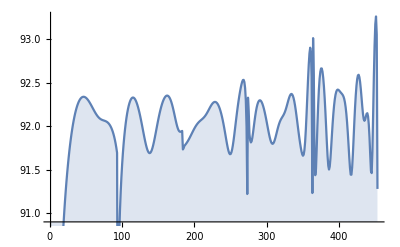

```mathematica
DiscretePlot[Log[outputPoint6Point7[[i]]],{i,1,Length[outputPoint6Point7]}](*This is with a functional = CombinedFunctional[11,{1,2,1/2},3,TwistSpinPairs[7/10,{10,8},1/10],6/10]*)
```

```mathematica
Module[{SDPBfunctional=SdpbList[TableOfDerivs[11,TwistSpinPairs[7/5,{10,8},1/10],51/100]],norm=NormScalingDimension[11,51/100],obj,outDir,func,out},obj=0*norm;outDir=SolveSDP[SDP[obj,norm,SDPBfunctional]];func=getFunctional[outDir,norm];out=SDPBfunctional.func;DiscretePlot[out[[i]],{i,Length[out]}]](*We want to continue to higher twists to see if negative by making twist symbolic.*)
```

-Graphics-

```mathematica
Module[{SDPBfunctional=SdpbList[TableOfDerivs[11,TwistSpinPairsHighDelta[7/5,{10,8},1/10],51/100]],norm=NormScalingDimension[11,51/100],obj,outDir,func,out},obj=0*norm;outDir=SolveSDP[SDP[obj,norm,SDPBfunctional]];func=getFunctional[outDir,norm];out=SDPBfunctional.func;DiscretePlot[out[[i]],{i,Length[out]}]]
```

-Graphics-

```mathematica
Module[{functional=tbSymbolic,positiveMatrices=SdpbList[tbPolynomialNew],norm=NormScalingDimension[11,51/100],obj,outDir,func,output,plots},obj=0*norm;outDir=solveSDP[SDP[obj,norm,positiveMatrices],{"--findPrimalFeasible","--findDualFeasible","--noFinalCheckpoint"}];func=getFunctional[outDir,norm];output=functional.func;plots=Table[Plot[output[[i]],{twist,1,12}],{i,1,Length[output]}]]
```

found dual feasible solution

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

found dual feasible solution

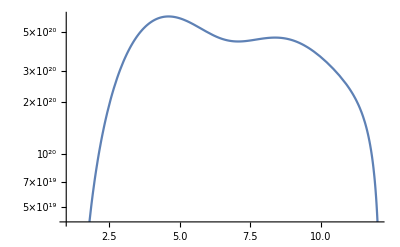
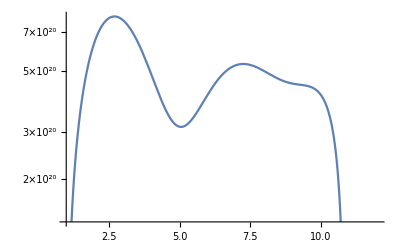
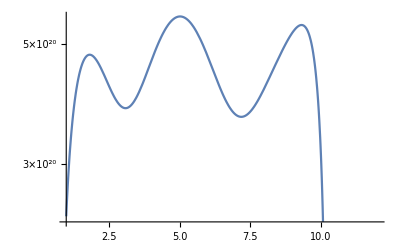
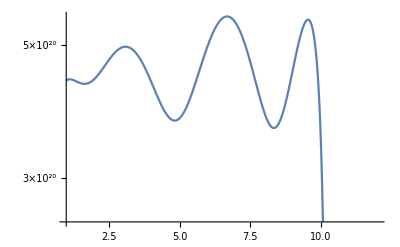
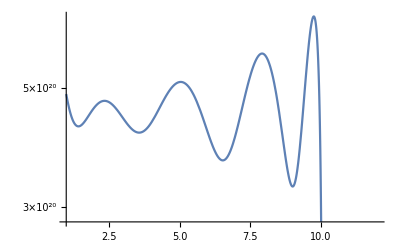

```mathematica
Module[{functional=tbSymbolic,positiveMatrices=SdpbList[tbPolynomialNew],norm=NormScalingDimension[11,51/100],obj,outDir,func,output,plots},obj=0*norm;outDir=solveSDP[SDP[obj,norm,positiveMatrices],{"--findPrimalFeasible","--findDualFeasible","--noFinalCheckpoint"}];func=getFunctional[outDir,norm];output=functional.func;plots=Table[LogPlot[output[[i]],{twist,1,12}],{i,1,Length[output]}]]
```

found dual feasible solution

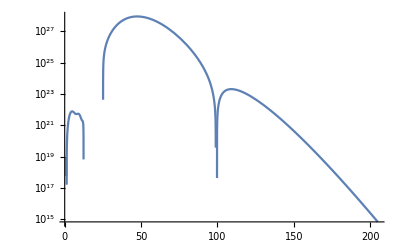
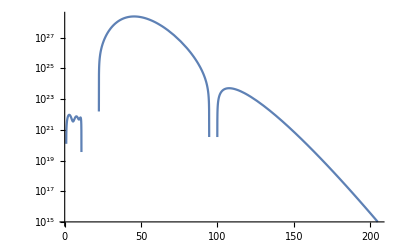
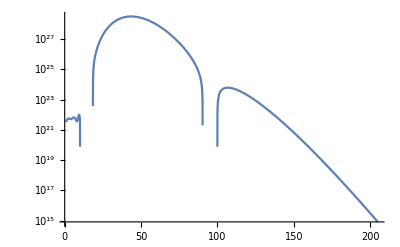
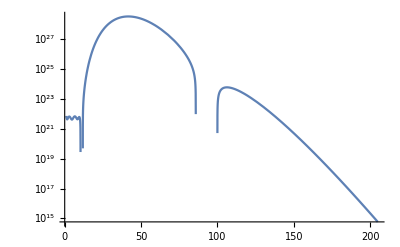
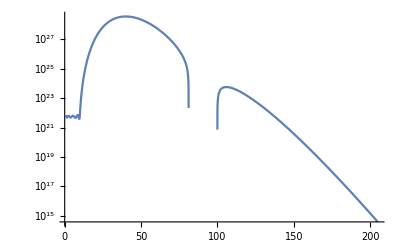

```mathematica
Module[{functional=tbSymbolic,positiveMatrices=SdpbList[tbPolynomialNewHighDelta],norm=NormScalingDimension[11,51/100],obj,outDir,func,output,plots},obj=0*norm;outDir=solveSDP[SDP[obj,norm,positiveMatrices],{"--findPrimalFeasible","--findDualFeasible","--noFinalCheckpoint"}];func=getFunctional[outDir,norm];output=functional.func;plots=Table[LogPlot[output[[i]],{twist,1,205}],{i,1,Length[output]}]]
```

```mathematica
Module[{functional=tbSymbolic,positiveMatrices=SdpbList[tbPolynomialNewHighDelta],norm=NormScalingDimension[11,51/100],obj,outDir,func,output,plots},obj=0*norm;outDir=solveSDP[SDP[obj,norm,positiveMatrices],{"--findPrimalFeasible","--findDualFeasible","--noFinalCheckpoint"}];func=getFunctional[outDir,norm];output=functional.func;plots=Table[Plot[output[[i]],{twist,1,205}],{i,1,Length[output]}]]
```

found dual feasible solution

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
(*Example of a binary search.*)Quiet[Close["/Users/michaelvenier-karzis/Desktop/Summer_2021_Research_Project/test.xml"]](*This is good to run in the same cell that you run a binary search so you don't get an error saying it's already open.*)
bootstrapBoundCombined[11,{1,2,1/2},3,10,8,1/10](*This would be a long computation. xf=5, twistMax=7 would reduce compuation time if you just want to test its functionality.*)
```

```mathematica
(*DeleteFile[] is sometimes good to use if you get an error associated with and outDir.*)
```

# Sample Calculations and Rough Work. No need to run this

## A values:

```mathematica
Table[A[3,j,2],{j,-1,5,2}];
```

```mathematica
Table[A[4,j,2],{j,-2,6,2}];
```

```mathematica
A[1,-1+l,l];
```

```mathematica
A[0,j,l];
```

```mathematica
Factor[A[1,l-1,l]];
```

```mathematica
Simplify[A[3,l-3,l]];
{A[5,3,0],A[4,2,0],A[3,1,0],A[2,0,0],A[1,-1,0],GammaP[Δ+2-1,-1],A[1,1,0],GammaM[Δ+2-1,0+1],E}(*This works after fixing GammaP from γ^+*)
```

{((-1+Δ)^2 Δ (2+Δ) (4+Δ)^2 (6+Δ)^2)/(4320 (1+Δ) (3+Δ) (-1+2 Δ)),((-1+Δ)^2 Δ (2+Δ) (4+Δ)^2)/(336 (1+Δ) (-1+2 Δ)),((-1+Δ)^2 Δ (2+Δ)^2)/(40 (1+Δ) (-1+2 Δ)),((-1+Δ)^2 Δ)/(12 (-1+2 Δ)),0,0,Δ/2,1/3 (-1+Δ)^2,ⅇ}

```mathematica
A[5,3,0]
```

((-1+Δ)^2 Δ (2+Δ) (4+Δ)^2 (6+Δ)^2)/(4320 (1+Δ) (3+Δ) (-1+2 Δ))

## Equations with s and ξ (with some comparisons)

```mathematica
{N[P[4,5,6,1]],N[Pcomplex[4,5,6,6]]}
```

{1296.,1296.}

```mathematica
{N[G[{3,2},1/2,1,7],25],N[G[{3,2},1/2,1,8],25]}(*How quickly does G converge?*)
```

{0.292362213134765625,0.2933007627725601196289063}

```mathematica
P[En,-1,s,ξ](*P works for negative j values*)
```

0

```mathematica
P[En,0,s,ξ](*P Works for j=0*)
```

s^En

```mathematica
G[{Δ,2},s,ξ,4];
```

```mathematica
Factor[D0[s,ξ][P[6,5,s,ξ]]/P[6,5,s,ξ]](*verifying equation 2.25*)
```

48

```mathematica
Collect[D2[s,ξ][G[{Δ,4},s,ξ,3]],{s,ξ},Factor];(*Using the D operator from 2.23*)
```

```mathematica
Collect[(Δ(Δ-2*(ν+1))+4(4+2*(ν+1)-2))*G[{Δ,4},s,ξ,3],{s,ξ},Factor];(*RHS of eigen equation*)
```

```mathematica
Collect[D2[s,ξ][G[{Δ,4},s,ξ,3]]-(Δ(Δ-2*(ν+1))+4(4+2*(ν+1)-2))*G[{Δ,4},s,ξ,3],{s,ξ},Factor](*Verifying 2.19 (eigen subtraction) (using s, ξ)*);
```

```mathematica
N[G[{31,20},1/2,1,12],25];
```

```mathematica
G[{4,1},1/2,1,9]===Gcomplex[{4,1},1/2,1/2,9]
```

False

```mathematica
D[F[{Δ1,l1},{z,zb},Δϕ],z];(*Leaving F implicit when taking derivs*)
```

## Equations with z and zb

```mathematica
Collect[(Δ(Δ-2*(ν+1))+4(4+2*(ν+1)-2))*Gcomplex[{Δ,4},z,zb,3],z,Factor];
```

```mathematica
Simplify[Collect[Dz[z,zb][Gcomplex[{Δ,4},z,zb,3]]-(Δ(Δ-2*(ν+1))+4(4+2*(ν+1)-2))*Gcomplex[{Δ,4},z,zb,3],z,Factor]]/.(z*zb)^(Δ/2):> ψ ;
Collect[%,z,Factor];(*Eigen subtraction to verify eq 2.19 now with z zb*)
```

```mathematica
Collect[Expand[((Δ(Δ-2*(ν+1))+4(4+2*(ν+1)-2))*Gcomplex[{Δ,4},z,zb,3]-Dz[z,zb][Gcomplex[{Δ,4},z,zb,3]])/((z*zb)^(Δ/2))],{z,zb},Factor];
```

```mathematica
D[Fexplicit[{1/2,0},z,zb,2,2],zb]/.{z:>1/2,zb:>1/2} (*This yeild indeterminate*)
```

Fexplicit^({0,0},0,1,0,0)[{1/2,0},1/2,1/2,2,2]

```mathematica
N[Gcomplex[{1,1},1/2,1/2,10]]
```

Gcomplex[{1.,1.},0.5,0.5,10.]

```mathematica
Pcomplextilda[En_,j_,z_,zb_]:=Boole[j>-1]*Sqrt[(1-z)(1-zb)]^En*(((j*Boole[j>-1])!)/Pochhammer[2*ν,j*Boole[j>-1]])*GegenbauerC[ν,j,(-z*zb+1+(1-z)(1-zb))/(2*Sqrt[(1-z)(1-zb)])](*Leading to an expression for g(v,u) instead of g(u,v)*)
```

```mathematica
Gcomplextilda[{Δ1_,l1_},z_,zb_,q_]:=Sum[A[n,l1+k,l1]*(Pcomplextilda[Δ1+n,l1+k,z,zb]),{n,0,q},{k,Max[-n,-l1],n,2}]/.{Δ:>Δ1,l:>l1}(*this is g(v,u)*)
```

```mathematica
{{Bnumerical[{0,0},{7,2},3,2]===Bnumerical[{0,0},{7,2},3,3]},{N[Gcomplex[{7,2},1/2,1/2,3,2],20]===N[Gcomplex[{7,2},1/2,1/2,3,3],20]}}
(*Seems like the problem is still there when switching other parameters*)(*seems fixed :)*)
```

{{False},{False}}

```mathematica
GcomplexLessOld[{twist_,l1_},z_,zb_,Δϕ_,q_]:=GcomplexLessOld[{twist,l1},z,zb,Δϕ,q]=Sum[A[n,l1+k,l1]*(Pcomplex[twist+l1+n,l1+k,z,zb]),{n,0,q},{k,If[OddQ[n],Max[-n,-l1+1],Max[-n,-l1]],n,2}]/.{Δ:>twist+l1,l:>l1}(*removed on July 12*)
```

```mathematica
N[D[GcomplexLessOld[{1,6},z,zb,51/100,7],{z,2},{zb,3}]/.{z:>1/2,zb:>1/2},200]
```

```mathematica
(*normalization*){Expand[GcomplexLessOld[{Δ-0,0},z,zb,51/100,0]/.zb:>z]}
```

{(z^2)^(Δ/2)}

```mathematica
(*normalization comparison*){Module[{l=4},GcomplexLessOld[{Δ-l,l},z,zb,51/100,0]/.zb:>z],FullSimplify[Module[{(*l=10,l1=10*)a=1},A[0,l1,l]*Pcomplex[En,l,z,zb]/.En:>twist+l1+n/.zb:>z/.n:>0/.Boole[l>-1]:>1(*/.Pochhammer[1,z]:>1*)/.LegendreP[__]:>1/.z!:>1/. l1:>l/.twist:>Δ-l]]}(*Norms agree.*)
```

LegendreP::argbu: LegendreP called with 1 argument; between 2 and 4 arguments are expected.

{(z^2)^(Δ/2),(z^2)^(Δ/2)}

## Implicit Table

```mathematica
(*Fstem[{Δ1_,l1_},{z_,zb_},Δϕ_,q_]:=(((1-z)(1-zb)))^Δϕ*Gstemcomplex[{Δ,l},{z,zb},Δϕ,q]-(z*zb)^Δϕ*Gstemcomplex[{Δ,l},{1-z,1-zb},Δϕ,q]*)
```

```mathematica
Table[Table[If[x≤y&& OddQ[x+y],D[Fstem[{Δ1,l1},{z,zb},Δϕ],{z,x},{zb,y}],0],{x,0,3},{y,0,3}],{l,0,3},{Δ,If[l>0,l+2*ν,Round[1/9+(2*(ν+1)-2)/2]],4}]/.{z:> 1/2,zb:>1/2} /. Derivative[{0,0},{x_,y_},0][B][{Δ_,l_},{1/2,1/2},q]:> B[x,y][Δ,l] /.B[{Δ_,l_},{1/2,1/2},q]:> B[0,0][Δ,l];(*this is the table of deriv's in implicit form with Fstem and not Bsstored. 0's are in the place of redundant derivs. B[x,y][Δ,l] represents the fucntion Fstem ([x,y] is the deriv order of z and zb respectively (with z=zb=1/2))*)
(*Here are the constraints: x+y must be odd, y ≥ x, unitary bounds on Delta: (for l > 0) Δ-d+2 = Δ≥ l+2*(ν+1)-2 for l=0 we have Δ ≥ (d-2)/2 = (2(ν+1)-2)/2 *)
```

```mathematica
XyTableImplicit[xf_]:=Table[If[x<y+1&&OddQ[x+y],D[Fstem[{Δ1,l1},{z,zb},Δϕ],{z,x},{zb,y}],Nothing],{x,0,xf},{y,0,xf}]/.{z:> 1/2,zb:>1/2} /. Derivative[{0,0},{x_,y_},0][B][{Δ_,l_},{1/2,1/2},q]:> B[x,y][Δ,l] /.B[{Δ_,l_},{1/2,1/2},q]:> B[0,0][Δ,l]
(*1 half of the 2 part table ie this is the columns of the combined table with Fstem*)
```

```mathematica
Table[Flatten[Table[If[x≤y&& OddQ[x+y],Bstored[x,y,Δ,l],Nothing],{x,0,3},{y,0,3}]],{l,0,3},{Δ,If[l>0,l+2*ν,Round[1/9+(2*(ν+1)-2)/2]],4}]/.{z:>1/2,zb:>1/2}/. Derivative[{0,0},{x_,y_},0][B][{Δ_,l_},{1/2,1/2},q]:> B[x,y][Δ,l] /.B[{Δ_,l_},{1/2,1/2},q]:> B[0,0][Δ,l];
(*This is the Bsstored version of the table of derivs with 0's in the place of the redundant elements. Not sure if 0's are preferable or if them just not existing is preferable.*)
```

```mathematica
Table[Table[If[x≤y&&OddQ[x+y],Bstored[x,y,Δ,l],Nothing[]],{x,0,3},{y,0,3}],{l,0,3},{Δ,If[l>0,l+2*ν,Round[1/9+(2*(ν+1)-2)/2]],4}]/.{z:>1/2,zb:>1/2}/. Derivative[{0,0},{x_,y_},0][Gstemcomplex][{Δ_,l_},{1/2,1/2},q]:> B[x,y][Δ,l] /.Gstemcomplex[{Δ_,l_},{1/2,1/2},q]:> B[0,0][Δ,l];
(*This is the Bsstored version of the table of derivs with the redundant elements (hopefully) deleted. ie the dimension of this matrix is lower than the matrix above*)
```

```mathematica
(*July 12*){XyTableStoredImplicit[3,{1,4},51/100,3](*Sort worked well it seems.*)[[3]],Collect[XyTableStoredImplicit[3,{1,4},51/100,3],B[__],Factor][[3]]}
```

{(127449 B[{0,0},{1,4},51/100,3])/(125000 2^(1/50))+(2703 B[{0,1},{1,4},51/100,3])/(2500 2^(1/50))-(51 B[{0,2},{1,4},51/100,3])/(50 2^(1/50))-(51 B[{1,1},{1,4},51/100,3])/(25 2^(1/50))+B[{1,2},{1,4},51/100,3]/2^(1/50),(127449 B[{0,0},{1,4},51/100,3])/(125000 2^(1/50))+(2703 B[{0,1},{1,4},51/100,3])/(2500 2^(1/50))-(51 B[{0,2},{1,4},51/100,3])/(50 2^(1/50))-(51 B[{1,1},{1,4},51/100,3])/(25 2^(1/50))+B[{1,2},{1,4},51/100,3]/2^(1/50)}

```mathematica
TableOfDerivsImplicit[xf_,Δϵ_,{twistMax_,lmax_},Δϕ_,q_,f_]:=TableOfDerivsImplicit[xf,Δϵ,{twistMax,lmax},Δϕ,q,f]=Table[XyTableStoredImplicit[xf,twistSpinPairs,Δϕ,q],{twistSpinPairs,TwistSpinPairs[Δϵ,{twistMax,lmax},f]}](*Make twistSpinPairs one argument for the caller.*)
```

```mathematica
TableOfDerivsImplicitOld[xf_,Δϵ_,twistMax_,lf_,Δϕ_,q_,f_]:=Flatten[Table[XyTableStoredImplicit[xf,{twist,l},Δϕ,q],{l,0,lf,2},{twist,If[l==0,Δϵ,1],twistMax,f}],{{1,2},{3}}]
```

```mathematica
XyTableImplicitPolynomial[xf_,{twist_,l_},Δϕ_,q_]:=XyTableImplicitPolynomial[xf,{twist,l},Δϕ,q]=Collect[Flatten[Table[If[x<y+1&&OddQ[x+y],Bstored[x,y,twist,l,Δϕ,q],Nothing],{x,0,xf},{y,0,xf}]]/.{Gstemcomplex[{twist,l},{z_,zb_},Δϕ,q]:>B[{0,0},{twist,l},{z,zb},Δϕ,q],Gstemcomplex[{twist,l},{1-z,1-zb},Δϕ,q]:>B[{0,0},{twist,l},{z,zb},Δϕ,q],Derivative[{0,0},{x_,y_},0,0][Gstemcomplex][{twist,l},{z_,zb_},Δϕ,q]:>B[Sort[{x,y}],{twist,l},{z,zb},Δϕ,q],Derivative[{0,0},{x_,y_},0,0][Gstemcomplex][{twist,l},{1-z,1-zb},Δϕ,q]:>If[OddQ[x+y],-B[Sort[{x,y}],{twist,l},{z,zb},Δϕ,q],B[Sort[{x,y}],{twist,l},{z,zb},Δϕ,q]]}/.{z:>1/2,zb:>1/2},B[__],Factor](*Is this necessary?*)
```

```mathematica
TwistListTrial[Δϵ_,twistMax_,j_,f_]:=Module[{table=Table[i,{i,11/10,twistMax,f}]},If[j==0,Table[i,{i,Δϵ,twistMax,f}],PrependTo[table,101/100]]](*This function is the list of twists that TableOfDerivsImplicit should be over.*)
```

```mathematica
TwistListTrialHighDelta[Δϵ_,twistMax_,j_,f_]:=Module[{table=Table[i,{i,If[j==0,Δϵ,11/10],twistMax,f}]},If[j==0,table,PrependTo[table,101/100]];AppendTo[table,100];AppendTo[table,200]]
```

```mathematica
TwistList[Δϵ_,Δmax_,j_,f_]:=Module[{table=Table[i,{i,11/10,Δmax-j,f}]},If[j==0,Table[i,{i,Δϵ,Δmax,f}],PrependTo[table,101/100]]](*This function is the list of twists that TableOfDerivsImplicit should be over.*)
```

```mathematica
TwistListHighDelta[Δϵ_,Δmax_,j_,f_]:=Module[{table=Table[i,{i,If[j==0,Δϵ,11/10],Δmax-j,f}]},If[j==0,table,PrependTo[table,101/100]];AppendTo[table,100-j];AppendTo[table,200-j]](*Same as above but with 2 high twist values added.*)
```

```mathematica
(*implement function to generate (twist,l) pairs. Keep both non high delta and high delta versions and make it easy to switch from one to the other. Make twistList an argument of the big functional function that I'm working on.*)
```

```mathematica
TableOfDerivsImplicitPolynomialTrial[xf_,Δϵ_,twistMax_,lf_,Δϕ_,q_,f_]:=TableOfDerivsImplicitPolynomialTrial[xf,Δϵ,twistMax,lf,Δϕ,q,f]=Flatten[Table[XyTableImplicitPolynomial[xf,{twist,l},Δϕ,q],{l,0,lf,2},{twist,TwistListTrial[Δϵ,twistMax,l,f]}(*If[twist+l<1,f,coarse] This doesn't work for some reason.*)],{{1,2},{3}}]
```

```mathematica
TableOfDerivsPolynomialTrial[]
```

```mathematica
TableOfDerivsImplicitPolynomialOld[xf_,Δϵ_,Δmax_,lf_,Δϕ_,q_,f_]:=TableOfDerivsImplicitPolynomialOld[xf,Δϵ,Δmax,lf,Δϕ,q,f]=Flatten[Table[XyTableImplicitPolynomial[xf,{twist,l},Δϕ,q],{l,0,lf,2},{twist,TwistList[Δϵ,Δmax,l,f]}(*If[twist+l<1,f,coarse] This doesn't work for some reason.*)],{{1,2},{3}}]
```

```mathematica
TableOfDerivsImplicitPolynomialHighDelta[xf_,Δϵ_,Δmax_,lf_,Δϕ_,q_,f_]:=TableOfDerivsImplicitPolynomialHighDelta=Flatten[Table[XyTableImplicitPolynomial[xf,{twist,l},Δϕ,q],{l,0,lf,2},{twist,TwistListHighDelta[Δϵ,Δmax,l,f]}(*If[twist+l<1,f,coarse] This doesn't work for some reason.*)],{{1,2},{3}}]
```

## Explicit Table

```mathematica
Bnumerical[{x_,y_},{twist_,l_},Δϕ_,q_]:=Bnumerical[{x,y},{twist,l},Δϕ,q]=N[D[GcomplexLessOld[{twist,l},z,zb,Δϕ,q],{z,x},{zb,y}]/.{z:>1/2,zb:>1/2},200](*No longer relavent.*)
```

```mathematica
{Bnumerical[{0,0},{9,8},1/2,3],N[Gcomplex[{9,8},1/2,1/2,1/2,3],20]}(*As expected.*)
```

{0.0180206298828125,0.0180206298828125}

```mathematica
{Bnumerical[{2,1},{3/2,3},7,10],Bnumerical[{2,1},{3/2,3},7,11]}(*Seeing how fast Bnumerical converges in q. for these values it seems we need q=11*)
```

{-2.676337610224650288586349699031548389023238361173610807034330124004370193809566472734939197016384692272721575944534976208316416028365484850334803445881836705143545300374614621464966768303425803113,-2.68102802395005675591263836635836595678314665708325657629851426310482551005263358214792396811139576396777772249887449880540889597396501548485427186060384214128607238939023233372069996752300917874}

```mathematica
BStoredExplicit[{x_,y_},{Δ_,l_},Δϕ_,q_]:= D[(((1-z)(1-zb)))^Δϕ*Gcomplex[{Δ,l},z,zb,Δϕ,q]-(z*zb)^Δϕ*Gcomplex[{Δ,l},1-z,1-zb,Δϕ,q],{z,x},{zb,y}]/.{z:>1/2,zb:>1/2}
```

```mathematica
(*Fexplicit[{Δ_,l_},z_,zb_,Δϕ_,q_]:=(((1-z)(1-zb)))^Δϕ*Gcomplex[{Δ,l},z,zb,Δϕ,q]-(z*zb)^Δϕ*Gcomplex[{Δ,l},1-z,1-zb,Δϕ,q]*)
```

```mathematica
D[Gcomplex[{9,6},z,zb,1/2,3]-Gcomplex[{9,6},z,zb,1/2,2],{z,0}]/.{z:>1/2,zb:>1/2}
```

13145/2228224

```mathematica
Clear[Gcomplex,Bstored,XyTableStoredImplicit,TableOfDerivsImplicit,Bnumerical,TableOfDerivsExplicitAttempt]
```

```mathematica
Clear[GcomplexTrial,BstoredTrial,XyTableStoredImplicitTrial,TableOfDerivsExplicitAttemptTrial,BnumericalTrial,TableOfDerivsExplicitAttemptTrial]
```

```mathematica
(*Here is all the functions that lead up to TableOfDerivsExplicitOld which is the way of constructing the table with Δ instead of twist.*)GcomplexOld[{Δ1_,l1_},z_,zb_,Δϕ_,q_]:=Sum[A[n,l1+k,l1]*(Pcomplex[Δ1+n,l1+k,z,zb]),{n,0,q},{k,If[OddQ[n],Max[-n,-l1+1],Max[-n,-l1]],n,2}]/.{Δ:>Δ1,l:>l1}(*Equation for conformal blocks using z and zb*)
(*backwards sum units of 2 from +n*)
(*Think about adapting binary search 2D code. This is for changing Δϕ and Δϵ (in spin 0 case). Find a way to make this run fast (could be ok already)*)
(*Tried to make the sum run backwards and yielded 0. therefore I made the If statement*)
```

```mathematica
Clear[BstoredOld,GcomplexOld,XyTableStoredImplicitOld,TableOfDerivsExplicitAttemptOld,TableOfDerivsImplicitOld,BnumericalOld]
```

```mathematica
BstoredOld[x_,y_,Δ_,l_,Δϕ_,q_]:= D[((1-z)(1-zb))^Δϕ*GstemcomplexOld[{Δ,l},{z,zb},Δϕ,q]-(z*zb)^Δϕ*GstemcomplexOld[{Δ,l},{1-z,1-zb},Δϕ,q],{z,x},{zb,y}](*...Added Δϕ dependence here...*)
```

```mathematica
XyTableStoredImplicitOld[xf_,{Δ_,l_},Δϕ_,q_]:=Flatten[Table[If[x<y+1&&OddQ[x+y],BstoredOld[x,y,Δ,l,Δϕ,q],Nothing],{x,0,xf},{y,0,xf}]]/.{z:> 1/2,zb:>1/2} (*/. Gstemcomplex^({0,0},{x_,y_},0)[{Δ_,l_},{1/2,1/2},q]:> B[x,y][Δ,l] /.Gstemcomplex[{Δ_,l_},{1/2,1/2},q]:> B[0,0][Δ,l]*)
```

```mathematica
TableOfDerivsImplicitOld[xf_,Δf_,lf_,Δϕ_,q_,f_]:=Flatten[Table[XyTableStoredImplicitOld[xf,{Δ,l},Δϕ,q],{l,0,lf,2},{Δ,If[l>0,Max[l+2*ν,7/5],Max[(2*(ν+1)-2)/2,7/5]],Δf,f}],{{1,2},{3}}](*Is this Δ bound correct? I see. the Δ bound makes the lack of l's make sense.*)
```

```mathematica
Import["tbbb.mx"][[19]][[30]]===tbbb[[19]][[30]](*Successfuly saved tbbb in a way that allows me to call the file tbbb as an expression.*)
```

True

```mathematica
Import["Derivs_Of_Gcomplex.mx"][[1]][[1]]===Gcomplex[{0,0},{7/5,0},1/2,1/2,51/100,17](*Saved Derivs of G complex in a matrix with the same formate as TableOfDerivsExplicitAttempt.*)
```

True

```mathematica
{Gcomplex[{4,7},{1,8},1/2,1/2,5,23],Gcomplex[{4,7},{1,8},1/2,1/2,5,22]}
100-100*(Min[%[[1]],%[[2]]]/Max[%[[1]],%[[2]]])

(*not a super high deriv order and q=23 is not good enough for 1% difference*)
```

{1.14931807924486014204587511257007139309389842640740653223474510014057159423828125×10^10,1.1118868119675564463882064036532321539378631580774481335538439452648162841796875×10^10}

3.25682402054418842347123892103556048660545731107141802452214992495486541424252452711100296842918322392926160596504371336643670219498633619310911972974456170907332047614535114858633148266837346422597

```mathematica
BnumericalOld[{x_,y_},{Δ_,l_},Δϕ_,q_]:=BnumericalOld[{x,y},{Δ,l},Δϕ,q]=N[D[GcomplexOld[{Δ,l},z,zb,Δϕ,q],{z,x},{zb,y}]/.{z:>1/2,zb:>1/2},200]
```

```mathematica
Export["tbbb.mx",tbbb](*Saving tbbb in a mathematica friendly way.*)
```

tbbb.mx

```mathematica
TableOfDerivsExplicitAttemptOld[xf_,{Δf_,lf_},Δϕ_,q_,f_]:=TableOfDerivsExplicitAttemptOld[xf,{Δf,lf},Δϕ,q,f]=TableOfDerivsImplicitOld[xf,Δf,lf,Δϕ,q,f]/.Derivative[{0,0},{x_,y_},0,0][GstemcomplexOld][{Δ_,l_},{1/2,1/2},Δϕ,q]:>BnumericalOld[{x,y},{Δ,l},Δϕ,q]/.GstemcomplexOld[{Δ_,l_},{1/2,1/2},Δϕ,q]:>GcomplexOld[{Δ,l},1/2,1/2,Δϕ,q]/.{}:>Nothing
(*look into SCH norm convention.*)(*# different slash dots #August 12*)
(*Exploring different /.'s {1-z,1-z}:>- vs going to 1/2,1/2 first.Not 100% sure if this is legit.*)FOldTwo[{m_,n_},{twist_,l_},Δϕ_,q_]:=Bstored[m,n,twist,l,Δϕ,q]/. {Gstemcomplex[{twist,l},{z,zb},Δϕ,q]:>B[{0,0},{twist,l},3,9,10],Derivative[{0,0},{x1_,y1_},0,0][Gstemcomplex][{twist,l},{z,zb},Δϕ,q]:>B[Sort[{x1,y1}],{twist,l},3,9,10]/.Derivative[{0,0},{x1_,y1_},0,0][Gstemcomplex][{twist,l},{1-z,1-zb},Δϕ,q]:>If[OddQ[x1+y1],-B[Sort[{x1,y1}],{twist,l},3,9,10],B[Sort[{x1,y1}],{twist,l},3,9,10]]}/.B[{m,n},{twist,l},3,9,10]:>GcomplexPolynomial[{m,n},{twist,l},3,9,10]/.{z:>1/2,zb:>1/2}(*Not sure why this doesn't work.*)
Gstemcomplex[{7,8},{1-z,1-zb},27/50,17]
(*Exploring different /.'s {1-z,1-z}:>- vs going to 1/2,1/2 first.Not 100% sure if this is legit. *)Module[{m=5,n=6,twist=7,spin=8,Δϕ=54/100,q=17},{FOldOne[{m,n},{twist,spin},Δϕ,q],F[{m,n},{twist,spin},Δϕ],FOldTwo[{m,n},{twist,spin},Δϕ,q]/.B[{a_,b_},{twist,spin},3,9,10]:>GcomplexPolynomial[{a,b},{twist,spin},3,9,10]/.Derivative[{0,0},{a_,b_},0,0][Gstemcomplex][{twist,spin},{1/2,1/2},27/50,17]:>GcomplexPolynomial[Sort[{a,b}],{twist,spin},3,9,10]/.Gstemcomplex[{twist,spin},{1/2,1/2},27/50,17]:>GcomplexPolynomial[{0,0},{twist,spin},3,9,10]}]
{6.5603937592864534651977829681994557209691138951870716199010554846048357699939273505941055186203062437437295490897153563156898095139503591905481355833781125765419044017584389711655825979310231236804452282691109401478761440176686781091212460246619847474432275842267787432437672082545744170713661671606947448625601141068272405896390524504955369447042429915679914`338.4812240342823*^11,6.5603937592864534651977829681994557209691138951870716199010554846048357699939273505941055186203062437437295490897153563156898095139503591905481355833781125765419044017584389711655825979310231236804452282691109401478761440176686781091212460246619847474432275842267787432437672082545744170713661671606947448625601141068272405896390524504955369447042429913133344`340.26668334773024*^11,6.5603937592864534651977829681994557209691138951870716199010554846048357699939273505941055186203062437437295490897153563156898095139503591905481355833781125765419044017584389711655825979310231236804452282691109401478761440176686781091212460246619847474432275842267787432437672082545744170713661671606947448625601141068272405896390524504955369447042429915679911`338.4812240342822*^11}
```

```mathematica
FOldOne[{m_,n_},{twist_,l_},Δϕ_,q_]:=Bstored[m,n,twist,l,Δϕ,q]/.{z:>1/2,zb:>1/2}/. {Gstemcomplex[{twist,l},{1/2,1/2},Δϕ,q]:>GcomplexPolynomial[{0,0},{twist,l},3,9,10],Derivative[{0,0},{x1_,y1_},0,0][Gstemcomplex][{twist,l},{1/2,1/2},Δϕ,q]:>GcomplexPolynomial[Sort[{x1,y1}],{twist,l},3,9,10]}
```

```mathematica
XyTableNumerical[xf_,{twist_,l_},Δϕ_,q_]:=XyTableNumerical[xf,{twist,l},Δϕ,q]=XyTableImplicit[xf,{twist,l},Δϕ](*Recall this is a collumn (or row?) of the matrix*)/.B[{x_,y_},{twist,l}]:>GcomplexNormedFast[{x,y},{twist,l},1/2,1/2,Δϕ,q](*/.Gstemcomplex^({0,0},{x_,y_},0,0)[{twist,l},{1/2,1/2},Δϕ,q]:>Bnumerical[{x,y},{twist,l},Δϕ,q]*)
```

```mathematica
TableOfDerivsExplicitAttempt[xf_,{Δϵ_,Δmax_,lf_},Δϕ_,q_,f_]:=TableOfDerivsExplicitAttempt[xf,{Δϵ,Δmax,lf},Δϕ,q,f]=Module[{table=TableOfDerivsImplicit[xf,Δϵ,Δmax,lf,Δϕ,q,f]},Monitor[Table[table[[i]]/.B[{x_,y_},{twist_,l_},Δϕ,q]:>GcomplexNormed[{x,y},{twist,l},1/2,1/2,Δϕ,q](*/.*)(*Gstemcomplex^({0,0},{x_,y_},0,0)[{twist_,l_},{1/2,1/2},Δϕ,q]:>Bnumerical[{x,y},{twist,l},Δϕ,q]*)(*/.{}:>Nothing*),{i,Length[table]}],{i,Length[table]}]]
(*/.Gstemcomplex[{twist_,l_},{1/2,1/2},Δϕ,q]:>Gcomplex[{twist,l},1/2,1/2,Δϕ,q]/.Gstemcomplex^({0,0},{x_,y_},0,0)[{twist_,l_},{1/2,1/2},Δϕ,q]:>Bnumerical[{x,y},{twist,l},Δϕ,q]/.{}:>Nothing*)
```

```mathematica
(*tbNew=TableOfDerivsImplict[11,7/5,9,8,51/100,17,1/10]/.B[{x_,y_},{twist_,l_},51/100,17]:>GcomplexNormed[{x,y},{twist,l},1/2,1/2,51/100,17];*)(*Export["tbNew.mx",tbNew]*)
tbNew=Import["/Users/michaelvenier-karzis/Desktop/Summer_2021_Research_Project/tbNew.mx"];
```

```mathematica
XyBlockTable[xf_,{twist_,l_},Δϕ_,q_]:=XyBlockTable[xf,{twist,l},Δϕ,q]=XyBlockTableImplicit[xf,{twist,l},Δϕ,q]/.Gstemcomplex[{x_,y_},{twist,l},1/2,1/2,Δϕ,17]:>GcomplexNormed[{x,y},{twist,l},1/2,1/2,Δϕ,17](*Columns of TableOfBlockDerivs.*)
```

```mathematica
TableOfBlockDerivs[xf_,{Δϵ_,Δmax_,lmax_},Δϕ_,q_,f_]:=TableOfBlockDerivs[xf,{Δϵ,Δmax,lmax},Δϕ,q,f]=Module[{table=TableOfBlockDerivsImplicit[xf,{Δϵ,Δmax,lmax},Δϕ,q,f]},Monitor[Table[table[[i]]/.Gstemcomplex[{x_,y_},{twist_,l_},1/2,1/2,51/100,q]:>GcomplexNormed[{x,y},{twist,l},1/2,1/2,51/100,q],{i,Length[table]}],{i,Length[table]}]](*Code for a table of derivs of Gcomplex.*)
```

```mathematica
(*derivsOfGcomplexNormed=*)TableOfBlockDerivs[11,{7/5,9,8},51/100,17,1/10](*This is the table of derivs of Gcomplex up to spin 8, 11 derivs and q=17*)
```

$Aborted

```mathematica
XyTablePolynomial[xf_,{twist_,l_},Δϕ_,q_:17]:=XyTablePolynomial[xf,{twist,l},Δϕ,q]=XyTableImplicitPolynomial[xf,{twist,l},Δϕ,q]/.B[{m_,n_},{twist,l},{1/2,1/2},Δϕ,17]:>GcomplexPolynomial[{m,n},{twist,l},3,9,10](*This works it just shouldn't have q as a variable. Can fix later.*)
```

```mathematica
TableOfDerivsExplicitPolynomial[xf_,Δϵ_,Δmax_,lf_,Δϕ_,q_:17,f_]:=TableOfDerivsExplicitPolynomial[xf,Δϵ,Δmax,lf,Δϕ,q,f]=Module[{table=TableOfDerivsImplicitPolynomial[xf,Δϵ,Δmax,lf,Δϕ,q,f]},Monitor[Table[table[[i]]/.B[{m_,n_},{twist_,j_},{1/2,1/2},Δϕ,17]:>GcomplexPolynomial[{m,n},{twist,j},3,9,10],{i,1,Length[table]}],{i,1,Length[table]}]](*This seems to work well again. It just doesn't need q. Can fix later. Annoying.*)
```

```mathematica
TableOfDerivsExplicitPolynomialHighDelta[xf_,Δϵ_,Δmax_,lf_,Δϕ_,q_,f_]:=TableOfDerivsExplicitPolynomialHighDelta[xf,Δϵ,Δmax,lf,Δϕ,q,f]=Module[{table=TableOfDerivsImplicitPolynomialHighDelta[xf,Δϵ,Δmax,lf,Δϕ,q,f]},Monitor[Table[table[[i]]/.B[{m_,n_},{twist_,j_},{1/2,1/2},Δϕ,17]:>GcomplexPolynomial[{m,n},{twist,j},3,9,10],{i,1,Length[table]}],{i,1,Length[table]}]]
```

```mathematica
tbPolynomialHighDelta=Import["/Users/michaelvenier-karzis/Desktop/Summer_2021_Research_Project/tbPolynomialHighDelta.mx"];(*=TableOfDerivsExplicitPolynomialHighDelta[11,7/5,10,8,51/100,17,1/10]*)
```

```mathematica
tbPolynomial=Import["/Users/michaelvenier-karzis/Desktop/Summer_2021_Research_Project/tbPolynomial.mx"];(*=TableOfDerivsExplicitPolynomial[11,7/5,10,8,51/100,17,1/10]*)
```

```mathematica
Export["Derivs_Of_Gcomplex.mx",TableOfBlockDerivs[11,{7/5,9,8},51/100,17,1/10]];(*Exporting the table of derivs of Gcomplex.*)
```

```mathematica
derivsOfGcomplexNormed=Import["/Users/michaelvenier-karzis/Desktop/Summer_2021_Research_Project/Derivs_Of_Gcomplex.mx"];
```

```mathematica
NormScalingDimensionOld[xf_,Δϕ_]:=NormScalingDimensionOld[xf,Δϕ]=XyTable[xf,{0,0},Δϕ,0]
```

## Numerical Experiments

```mathematica
{GcomplexPolynomial[{4,9},{40,8},3,9,10],GcomplexNormed[{4,9},{40,8},1/2,1/2,51/100,25]}(*This comparison holds well at twist=8, l=8 and moderate deriv orders. Even up to [{4,7},{8,8},Δϕ,25] there is 5% agreement. when deriv order starts to get pushed. They agree well for pretty large twists. but as twist gets very large they start to differ a lot.*)
(*It seems like the expensive thing for Gcomplex is deriv order. not twist.*)(*Δ Can be varied easily here.*)(*It really breaks down when you get to [{10,11},{2,4},1/2,1/2,51/100,25]*)
%[[1]]/%[[2]]
```

{3.2866795462081726184841733393639832295444707180081868029876197573039328509189674849780678039204300107280582681576210998772064186066995613003553532068583159606294749274862360968936213714135733172142859692943368889281966980631353217826807747413183371508574015084818263090508956330696486228545161047825996279744190562796450438418509243×10^16,1.2023299683521201629429334916311958821721714149487451823851468687396925799247865290904969888498058188206075201685170726700741513884871852533048132506658443804432354266775541745047557796591303176962889×10^16}

2.7335919695263054183101557622380552999545985213144006740051835099166562704087392401550326848109208824417438464781585503861791505293239815358439234410893322766494894956736229980732046831473807944406706